# Managing thermal guild interactions in warming food webs

## Initialization

## Model

tyler had different attack rate for walleye on new resource (RA1), but didn’t add it to params list, so I added it to params list, but kept it the same as others (to start)

```mathematica
Clear[fR1,fC1,fJ1,fP1,fP2,fR2]
fR1[R1_,C1_,J1_]:= rmax*R1*(1-R1/K1)- aJ1[T]*R1*J1-aC1[T]*R1*C1 
fC1[R1_,C1_,P1_,P2_]:= aC1[T]*R1*C1-aP1c1[T]*C1*P1 - aP2c1[T]*C1*P2 - mC1[T]*C1 - h4*C1
fJ1[R1_,C1_,J1_,P1_,P2_,R2_]:= (αw2*(1-som)*((aP1c1[T]*C1*P1)+(aP1r2[T]*R2*P1)))/(1+βw1*(1-som)*((aP1c1[T]*C1*P1)+(aP1r2[T]*R2*P1)))+ (1-mat)*(aJ1[T]*R1*J1) - aP2j1[T]*J1*P2 - mJ1[T]*J1 - h2*J1
fP1[R1_,C1_,J1_,P1_,R2_]:= mat*(aJ1[T]*R1*J1) + som*aP1c1[T]*C1*P1 + som*aP1r2[T]*R2*P1 - mP1[T]*P1 - h1*P1 
fP2[C1_,P2_,J1_]:= aP2c1[T]*C1*P2 + aP2j1[T]*J1*P2 - mP2[T]*P2 - h3*P2
fR2[P1_,R2_]:= rmax2*R2*(1-R2/K2) - aP1r2[T]*R2*P1
(*(1-R2/K2)*)
```

```mathematica
Clear[PdSystem]
PdSystem[{R10_, C10_, J10_, P10_, P20_, R20_}] := {
 R1'[t]== fR1[R1[t],C1[t],J1[t]],
 C1'[t]== fC1[R1[t],C1[t],P1[t],P2[t]],
 J1'[t]== fJ1[R1[t],C1[t],J1[t],P1[t],P2[t],R2[t]],
 P1'[t]== fP1[R1[t],C1[t],J1[t],P1[t],R2[t]], 
 P2'[t]== fP2[C1[t],P2[t],J1[t]],
 R2'[t]== fR2[R2[t],P1[t]],
 R1[0]==R10, 
 C1[0]==C10, 
 J1[0]==J10, 
 P1[0]==P10, 
 P2[0]==P20,
 R2[0]== R20
 };
```

## Parameters

Here, “rates” are the temperature-independent variables and “params” are the base values for the temperature-dependent variables. NOTE that I switched scenarios 1 and 2. so the new scenario 1 will have rates2 and params2 because it use to be scenario 1. However, this is consistent with the TPCs and the “Scenario 1” and “Scenario 2” sections, so just leave it for now.

```mathematica
Clear[rates, params]
rates = Dispatch[{
som -> 0.8,
mat -> 0.65, (*0.65*)
αw2 -> 1,
βw1 -> 0.0025, (*can use 0.0025 like Ogle 2013 (fishR) and get the same result - tested in "betatest" notebook---used 1.0 before with same results*)
rmax -> 1,
K1 -> 10,
h1-> 0.15, (*P1 harvest*)
h2-> 0.0, (*J1 harvest*)
h3-> 0.15, (*P2 harvest*)
h4-> 0.01, (*C1 harvest*)
K2 -> 7.5, (*changing this to 10 makes it so that there is no difference between bass presence/absence on the walleye population. Probably because walleye have enough resources regardless of trophic control*)
rmax2 -> 0.1 (*testing up to 10 to see if that makes population stay above zero and it didn't change the biomass plot, so something is weird here...*)
(*v1 -> 0.3,
u1 -> 0.3,
h1 -> 0, (*Subscript[R, 2] harvest*)*)
}];

(*for TPC functions*)
params = Dispatch[{
σ -> 5, (*increasing makes slope shallower*)
σ2 -> 1, (*increasing makes slope shallower*)

ap1c1 -> 0.02, (*P1 attack on C1, FB4 0.0387,0.04*)
ap1r2 -> 0.005, (*P1 attack on R2*)
aj1 -> 0.08, (*J1 attack on resource, FB4 0.13*)
ac1 -> 0.08, (*C1 attack on resource, FB4 0.052*)
ap2c1 -> 0.02, (*P2 attac on C1, FB4 0.035*,0.04*)
ap2j1 -> 0.00, (*P2 attack on J1- change back to 0.001 if plots look weird*)

mp1 -> 0.004, (*0.001*)
mj1 -> 0.006, (*0.002*)
mp2 -> 0.004, 
mc1 -> 0.005, 

Topt1 -> 22, (* P1 optimal temp (adult Walleye) - from FB4*)
Topt2 -> 25, (* J1 optimal temp (juv Walleye) - from FB4*)
Topt3 -> 27.5, (* P2 optimal temp (largemouth bass)- from FB4; Smallmouth would be 29 *)
Topt4 -> 27, (* C1 optimal temp (bluegill) - from FB4*)

Tmax1 -> 28, (* P1 optimal temp (adult Walleye) - from FB4*)
Tmax2 -> 28, (* J1 optimal temp (juv Walleye) - from FB4*)
Tmax3 -> 37, (* P2 optimal temp (Largemouth Bass)- from FB4; Smallmouth would be 36 *)
Tmax4 -> 36, (* C1 optimal temp (Bluegill) - from FB4*)

T->25
}];
```

## Thermal Performance Curves (TPCs)

### Piecewise Functions

Temperature curves for P1, J1, P2, and C1 attack rate

```mathematica
Clear[aP1c1,aP1r2,aJ1,aC1,aP2c1,aP2j1]

(*P1 attack rate on C1*)
aP1c1[T_]:=ap1c1*Piecewise[{
{Exp[-((T-Topt1)/(2 σ))^2],T<Topt1},
{1-((T-(Topt1))/((Topt1)-Tmax1))^2,Tmax1>T≥Topt1},
{0,T≥Tmax1}
}];

(*P1 attack rate on R2*)
aP1r2[T_]:=ap1r2*Piecewise[{
{Exp[-((T-Topt1)/(2 σ))^2],T<Topt1},
{1-((T-(Topt1))/((Topt1)-Tmax1))^2,Tmax1>T≥Topt1},
{0,T≥Tmax1}
}];

(*J1 attack rate on R1*)
aJ1[T_]:=aj1*Piecewise[{
{Exp[-((T-Topt2)/(2 σ))^2],T<Topt2},
{1-((T-(Topt2))/((Topt2)-Tmax2))^2,Tmax2>T≥Topt2},
{0,T≥Tmax2}
}];

(*bass attack rates on C1*)
aP2c1[T_]:=ap2c1*Piecewise[{
{Exp[-((T-Topt3)/(2 σ))^2],T<Topt3},
{1-((T-(Topt3))/((Topt3)-Tmax3))^2,Tmax3>T≥Topt3},
{0,T≥Tmax3}
}];

(*bass attack rates on J1*)
aP2j1[T_]:=ap2j1*Piecewise[{
{Exp[-((T-Topt3)/(2 σ))^2],T<Topt3},
{1-((T-(Topt3))/((Topt3)-Tmax3))^2,Tmax3>T≥Topt3},
{0,T≥Tmax3}
}];

(*consumer attack rate on R1*)
aC1[T_]:= ac1*Piecewise[{
{Exp[-((T-Topt4)/(2 σ))^2],T<Topt4},
{1-((T-(Topt4))/((Topt4)-Tmax4))^2,Tmax4>T≥Topt4},
{0,T≥Tmax4}
}];
```

Temperature curves for P1, J1, P2, and C1 mortality rate

```mathematica
(*Note that these can be adjusted to eith warm or cool by changing Tmax *)
Clear[mP1,mJ1,mP2,mC1] 
mP1[T_]:= Piecewise[{
{mp1*T, T≤10},
{mp1*T+mp1*Exp[((T-Tmax1)/σ2)], 10<T}
}]; 
mJ1[T_]:= Piecewise[{ 
{mj1*T, T≤10},
{mj1*T+mj1*Exp[((T-Tmax2)/σ2)], 10<T}
}]; 
mP2[T_]:= Piecewise[{
{mp2*T,T≤10},
{mp2*T+mp2*Exp[((T-Tmax3)/σ2)], 10<T}
}]; 
mC1[T_]:= Piecewise[{
{mc1*T, T≤10},
{mc1*T+mc1*Exp[((T-Tmax4)/σ2)], 10<T}
}];
```

### TPCs

Attack (consumption) rates

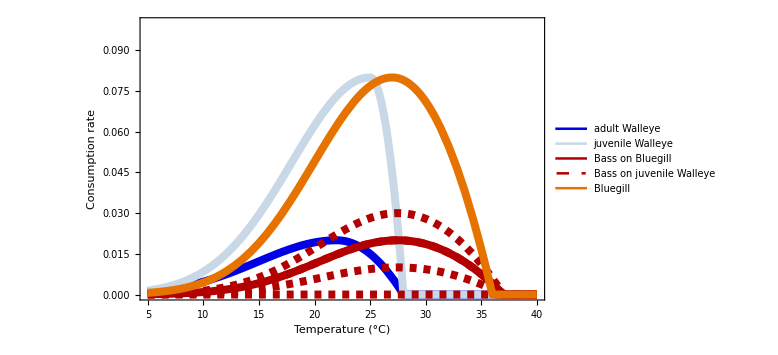

```mathematica
Plot[{aP1c1[Tx]/.params, aJ1[Tx]/.params, aP2c1[Tx]/.params, aP2j1[Tx]/.params, aP2j1[Tx]/.ap2j1->0.01/.params, aP2j1[Tx]/.ap2j1->0.02/.params, aP2j1[Tx]/.ap2j1->0.03/.params, aC1[Tx]/.params},{Tx,5,40}, PlotRange->{{5,40},{0,0.10}}, PlotLegends->{"adult Walleye", "juvenile Walleye", "Bass on Bluegill", "Bass on juvenile Walleye", "", "", "", "Bluegill"}, Frame->True, 
FrameLabel->{{"Consumption rate",""},{"Temperature (°C)",""}}, PlotStyle -> {{Thickness[0.01],Darker[Blue,0.1]},{Thickness[0.01],Darker[LightBlue,0.1]}, {Thickness[0.01], Darker[Red,0.3]}, {Thickness[0.01], Dashed, Darker[Red,0.3]}, {Thickness[0.01], Dashed, Darker[Red,0.3]}, {Thickness[0.01], Dashed, Darker[Red,0.3]}, {Thickness[0.01], Dashed, Darker[Red,0.3]}, {Thickness[0.01], Darker[Orange,0.1]}}, 
ImageSize->Large, LabelStyle->Directive[FontSize->20, FontFamily->"Arial", FontColor->"Black"]]
```

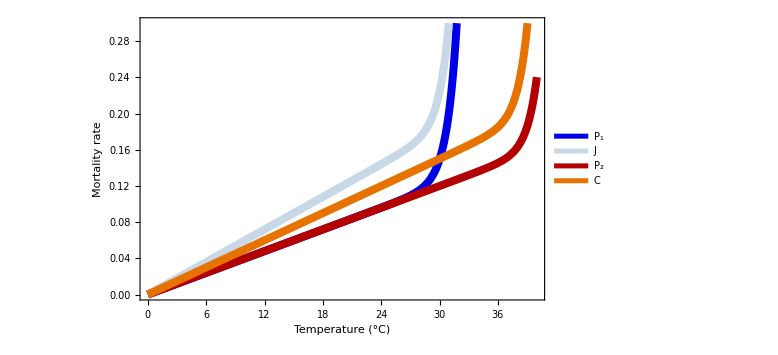

```mathematica
Plot[{mP1[Tx]/.params, mJ1[Tx]/.params, mP2[Tx]/.params, mC1[Tx]/.params },{Tx,0,40}, PlotLegends->{"P_1","J","P_2","C"}, PlotRange->{{0,40},{0,0.3}}, Frame->True, 
FrameLabel->{{"Mortality rate",""},{"Temperature (°C)",""}}, PlotStyle ->{{Thickness[0.01],Darker[Blue,0.1]},{Thickness[0.01],Darker[LightBlue,0.1]}, {Thickness[0.01], Darker[Red,0.3]}, {Thickness[0.01], Darker[Orange,0.1]}}, 
ImageSize->Large, LabelStyle->Directive[FontSize->20, FontFamily->"Arial", FontColor->"Black"]]
```

Attack rate TPC for different consumers (Yellow Perch, Golden Shiner, Black Crappie, Pumpkinseed)

## Main Results

## P_1 & J_1 are cool-water P_2 & C_1 are warm-water. P_1 and P_2 eat C_1 and C_1 and J_1 eat R_1. No predation on J_1. In manuscript

## Biomass Trends

### P_1

```mathematica
Clear[bifMean]
bifMean=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->val/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,val,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{val,0,40,1},{hin,0,1,0.1}]],2];
```

```mathematica
(* Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
Clear[P1h0,P1h1,P1h2,P1h3,P1h4]
P1h0 =Take[bifMean[[All,2;;3]],{1,Length[bifMean],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the first h of each (i.e. h=0.0)*)
P1h1 =Take[bifMean[[All,2;;3]],{2,Length[bifMean],11}];(*plot positions 2 and 3 (i.e. temperature and biomass) for the second h of each (i.e. h=0.1)*)
P1h2 =Take[bifMean[[All,2;;3]],{3,Length[bifMean],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the third h of each (i.e. h=0.2)*)
P1h3 =Take[bifMean[[All,2;;3]],{4,Length[bifMean],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the forth h of each (i.e. h=0.3)*)
P1h4 =Take[bifMean[[All,2;;3]],{5,Length[bifMean],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the fifth h of each (i.e. h=0.4)*)
```

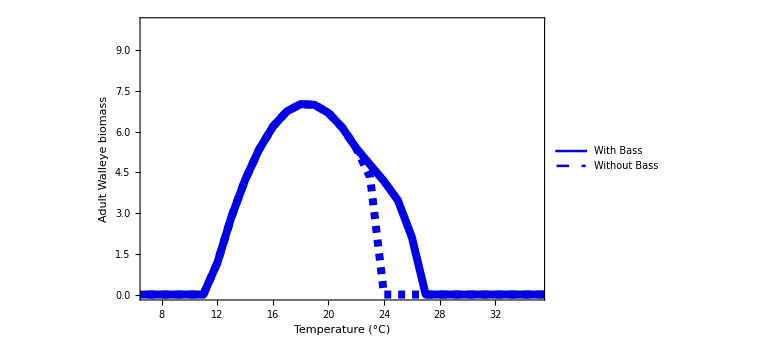

```mathematica
Clear[P1plot]
P1plot=ListLinePlot[{P1h0,P1h4}, PlotRange->{{7,35},{0,10}}, Frame->True, FrameLabel->{{"Adult Walleye biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"With Bass", "Without Bass"},
PlotStyle -> {{Thickness[0.01], Darker[Blue,0.1]},{Thickness[0.01], Dashed, Darker[Blue,0.1]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, FontFamily->"Arial", FontColor->"Black"]]
```

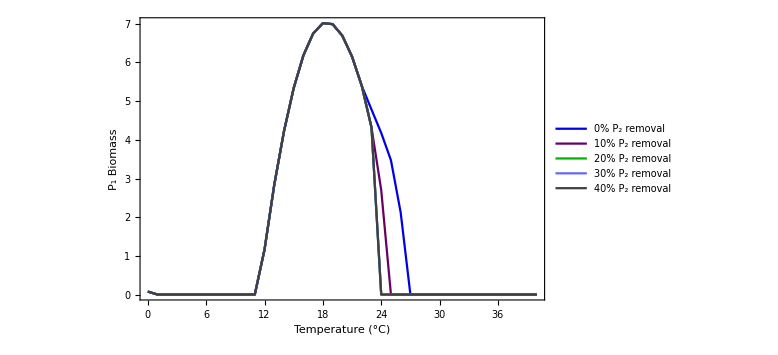

```mathematica
Clear[P1plot2]
P1plot2=ListLinePlot[{P1h0,P1h1,P1h2,P1h3,P1h4}, PlotRange->{{0,40},All}, Frame->True, FrameLabel->{{"P_1 Biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"0% P_2 removal", "10% P_2 removal", "20% P_2 removal", "30% P_2 removal", "40% P_2 removal"},
PlotStyle -> {Darker[Blue,0.1],Darker[Purple,0.2],Darker[Green,0.3],Lighter[Blue,0.4],Darker[Gray,0.5]}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

change Tmax4 & Topt (values taken from  Hasnain 2013 supplement)
b Yellow Perch :  Tmax4 = 35; Topt4 = 25 (28 & 23 C from FB4, respectively
c Golden Shiner : Tmax4 = 32; Topt4 = 25
d Black Crappie : Tmax4 = 34.9; Topt4 = 18
e Pumpkinseed : Tmax4 = 37.6; Topt4 = 25

#### b; C_1 = Yellow Perch

```mathematica
Clear[bifMeanb] (*yellow perch as consumer*)
bifMeanb=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->val/.Tmax4->35/.Topt4->25/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,val,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{val,0,40,1},{hin,0,1,0.1}]],2];
```

```mathematica
(* Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
Clear[P1h0b,P1h1b,P1h2b,P1h3b,P1h4b]
P1h0b =Take[bifMeanb[[All,2;;3]],{1,Length[bifMeanb],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the first h of each (i.e. h=0.0)*)
P1h1b =Take[bifMeanb[[All,2;;3]],{2,Length[bifMeanb],11}];(*plot positions 2 and 3 (i.e. temperature and biomass) for the second h of each (i.e. h=0.1)*)
P1h2b =Take[bifMeanb[[All,2;;3]],{3,Length[bifMeanb],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the third h of each (i.e. h=0.2)*)
P1h3b =Take[bifMeanb[[All,2;;3]],{4,Length[bifMeanb],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the forth h of each (i.e. h=0.3)*)
P1h4b =Take[bifMeanb[[All,2;;3]],{5,Length[bifMeanb],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the fifth h of each (i.e. h=0.4)*)
```

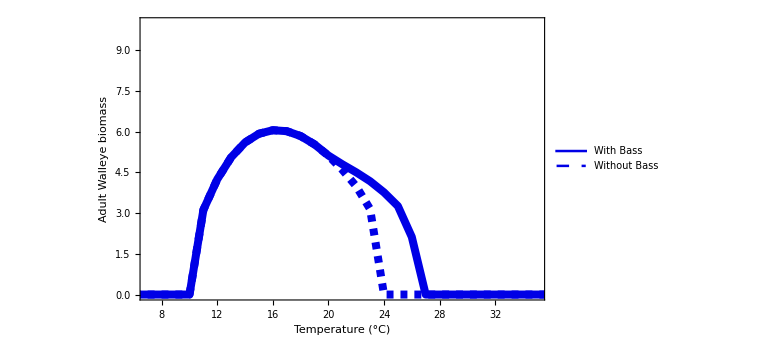

```mathematica
Clear[P1plotb]
P1plotb=ListLinePlot[{P1h0b,P1h4b}, PlotRange->{{7,35},{0,10}}, Frame->True, FrameLabel->{{"Adult Walleye biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"With Bass", "Without Bass"},
PlotStyle -> {{Thickness[0.01], Darker[Blue,0.1]},{Thickness[0.01], Dashed, Darker[Blue,0.1]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, FontFamily->"Arial", FontColor->"Black"]]
```

#### c; C_1 = Golden Shiner

```mathematica
Clear[bifMeanc] (*golden shiner as consumer*)
bifMeanc=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->val/.Tmax4->32/.Topt4->25/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,val,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{val,0,40,1},{hin,0,1,0.1}]],2];
```

```mathematica
(* Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
Clear[P1h0c,P1h1c,P1h2c,P1h3c,P1h4c]
P1h0c =Take[bifMeanc[[All,2;;3]],{1,Length[bifMeanc],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the first h of each (i.e. h=0.0)*)
P1h1c =Take[bifMeanc[[All,2;;3]],{2,Length[bifMeanc],11}];(*plot positions 2 and 3 (i.e. temperature and biomass) for the second h of each (i.e. h=0.1)*)
P1h2c =Take[bifMeanc[[All,2;;3]],{3,Length[bifMeanc],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the third h of each (i.e. h=0.2)*)
P1h3c =Take[bifMeanc[[All,2;;3]],{4,Length[bifMeanc],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the forth h of each (i.e. h=0.3)*)
P1h4c =Take[bifMeanc[[All,2;;3]],{5,Length[bifMeanc],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the fifth h of each (i.e. h=0.4)*)
```

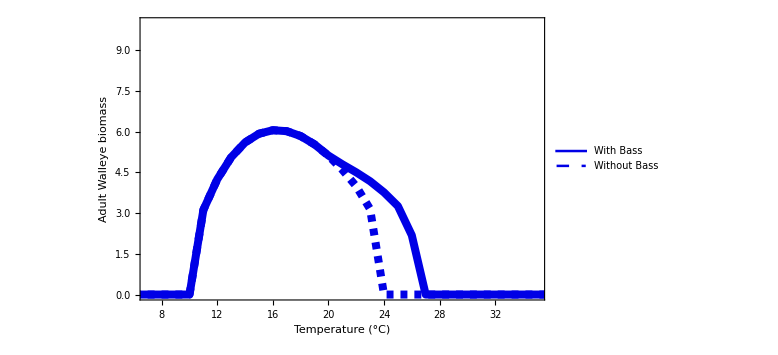

```mathematica
Clear[P1plotc]
P1plotc=ListLinePlot[{P1h0c,P1h4c}, PlotRange->{{7,35},{0,10}}, Frame->True, FrameLabel->{{"Adult Walleye biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"With Bass", "Without Bass"},
PlotStyle -> {{Thickness[0.01], Darker[Blue,0.1]},{Thickness[0.01], Dashed, Darker[Blue,0.1]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, FontFamily->"Arial", FontColor->"Black"]]
```

#### d; C_1 = Black Crappie

```mathematica
Clear[bifMeand] (*golden shiner as consumer*)
bifMeand=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->val/.Tmax4->34.9/.Topt4->18/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,val,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{val,0,40,1},{hin,0,1,0.1}]],2];
```

```mathematica
(* Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
Clear[P1h0d,P1h1d,P1h2d,P1h3d,P1h4d]
P1h0d =Take[bifMeand[[All,2;;3]],{1,Length[bifMeand],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the first h of each (i.e. h=0.0)*)
P1h1d =Take[bifMeand[[All,2;;3]],{2,Length[bifMeand],11}];(*plot positions 2 and 3 (i.e. temperature and biomass) for the second h of each (i.e. h=0.1)*)
P1h2d =Take[bifMeand[[All,2;;3]],{3,Length[bifMeand],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the third h of each (i.e. h=0.2)*)
P1h3d =Take[bifMeand[[All,2;;3]],{4,Length[bifMeand],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the forth h of each (i.e. h=0.3)*)
P1h4d =Take[bifMeand[[All,2;;3]],{5,Length[bifMeand],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the fifth h of each (i.e. h=0.4)*)
```

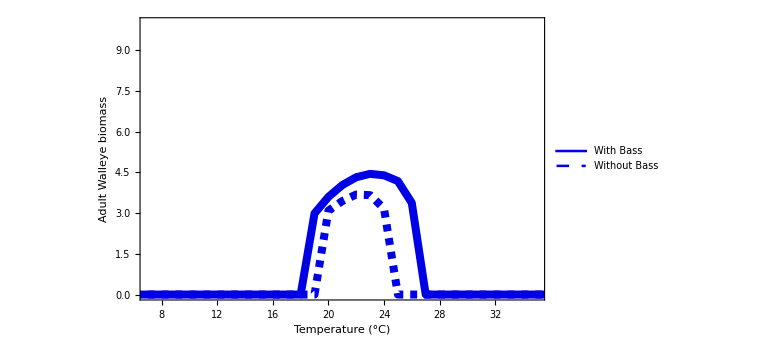

```mathematica
Clear[P1plotd]
P1plotd=ListLinePlot[{P1h0d,P1h4d}, PlotRange->{{7,35},{0,10}}, Frame->True, FrameLabel->{{"Adult Walleye biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"With Bass", "Without Bass"},
PlotStyle -> {{Thickness[0.01], Darker[Blue,0.1]},{Thickness[0.01], Dashed, Darker[Blue,0.1]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, FontFamily->"Arial", FontColor->"Black"]]
```

#### e; C_1 = Pumpkinseed

```mathematica
Clear[bifMeane] (*golden shiner as consumer*)
bifMeane=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->val/.Tmax4->37.6/.Topt4->25/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,val,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{val,0,40,1},{hin,0,1,0.1}]],2];
```

```mathematica
(* Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
Clear[P1h0e,P1h1e,P1h2e,P1h3e,P1h4e]
P1h0e =Take[bifMeane[[All,2;;3]],{1,Length[bifMeane],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the first h of each (i.e. h=0.0)*)
P1h1e =Take[bifMeane[[All,2;;3]],{2,Length[bifMeane],11}];(*plot positions 2 and 3 (i.e. temperature and biomass) for the second h of each (i.e. h=0.1)*)
P1h2e =Take[bifMeane[[All,2;;3]],{3,Length[bifMeane],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the third h of each (i.e. h=0.2)*)
P1h3e =Take[bifMeane[[All,2;;3]],{4,Length[bifMeane],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the forth h of each (i.e. h=0.3)*)
P1h4e =Take[bifMeane[[All,2;;3]],{5,Length[bifMeane],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the fifth h of each (i.e. h=0.4)*)
```

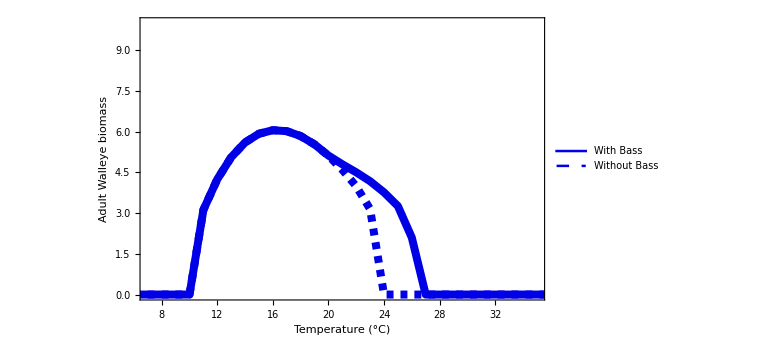

```mathematica
Clear[P1plote]
P1plote=ListLinePlot[{P1h0e,P1h4e}, PlotRange->{{7,35},{0,10}}, Frame->True, FrameLabel->{{"Adult Walleye biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"With Bass", "Without Bass"},
PlotStyle -> {{Thickness[0.01], Darker[Blue,0.1]},{Thickness[0.01], Dashed, Darker[Blue,0.1]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, FontFamily->"Arial", FontColor->"Black"]]
```

### J_1

```mathematica
Clear[bifMeanJ1]
bifMeanJ1=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->val/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,val,Chop[Mean[J1[Range[4000,5000]]]/.sol1,10^-2]}],{val,5,40,1},{hin,0,1,0.1}]],2];
```

```mathematica
(* Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
Clear[J1h0,J1h1]
J1h0 =Take[bifMeanJ1[[All,2;;3]],{1,Length[bifMeanJ1],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the second h of each (i.e. h=0.1)*)
J1h1 =Take[bifMeanJ1[[All,2;;3]],{2,Length[bifMeanJ1],11}];
J1h2 =Take[bifMeanJ1[[All,2;;3]],{3,Length[bifMeanJ1],11}];
J1h3 =Take[bifMeanJ1[[All,2;;3]],{4,Length[bifMeanJ1],11}];
J1h4 =Take[bifMeanJ1[[All,2;;3]],{5,Length[bifMeanJ1],11}];
```

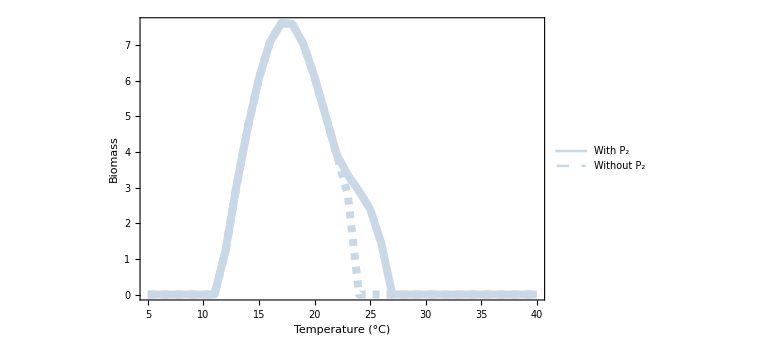

```mathematica
Clear[J1plot]
J1plot=ListLinePlot[{J1h0,J1h4}, PlotRange->{{5,40},All}, Frame->True, FrameLabel->{{"Biomass", ""}, {"Temperature (°C)", "cool-water juvenile biomass"}}, PlotLegends->{"With P_2", "Without P_2"},
PlotStyle -> {{Thickness[0.01], Darker[LightBlue,0.1]}, {Thickness[0.01], Dashed, Darker[LightBlue,0.1]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

### P_2

```mathematica
Clear[bifMeanP2]
bifMeanP2=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->val/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,val,Chop[Mean[P2[Range[4000,5000]]]/.sol1,10^-2]}],{val,5,40,1},{hin,0,1,0.1}]],2];
```

General::munfl: (6.68617×10^-306)/1001 is too small to represent as a normalized machine number; precision may be lost.

```mathematica
(* Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
Clear[P2h0,P2h1]
P2h0 =Take[bifMeanP2[[All,2;;3]],{1,Length[bifMeanP2],11}] (*plot positions 2 and 3 (i.e. temperature and biomass) for the second h of each (i.e. h=0.1)*)
P2h1 =Take[bifMeanP2[[All,2;;3]],{2,Length[bifMeanP2],11}]; 
P2h2 =Take[bifMeanP2[[All,2;;3]],{3,Length[bifMeanP2],11}];
P2h3 =Take[bifMeanP2[[All,2;;3]],{4,Length[bifMeanP2],11}]; 
P2h4 =Take[bifMeanP2[[All,2;;3]],{5,Length[bifMeanP2],11}](*5 is h=0.2*)
```

{{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,1.61385},{24,3.89163},{25,6.35868},{26,10.9086},{27,15.4653},{28,14.5174},{29,13.4075},{30,12.0928},{31,10.4867},{32,8.41431},{33,5.4893},{34,0.702797},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0}}

{{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0}}

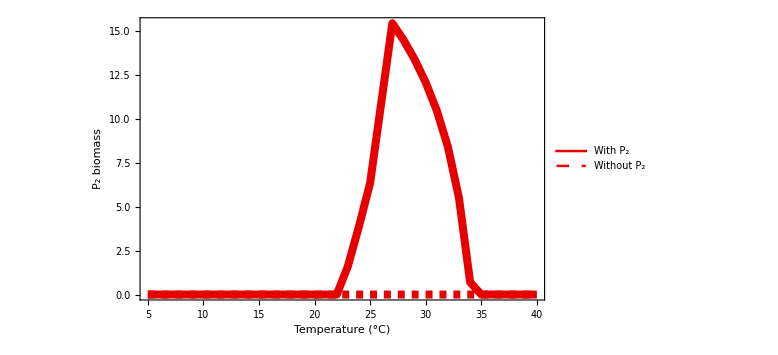

```mathematica
Clear[P2plot]
P2plot=ListLinePlot[{P2h0,P2h4}, PlotRange->{{5,40},All}, Frame->True, FrameLabel->{{"P_2 biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"With P_2", "Without P_2"},
PlotStyle -> {{Thickness[0.01],Darker[Red,0.1]},{Thickness[0.01],Dashed,Darker[Red,0.1]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

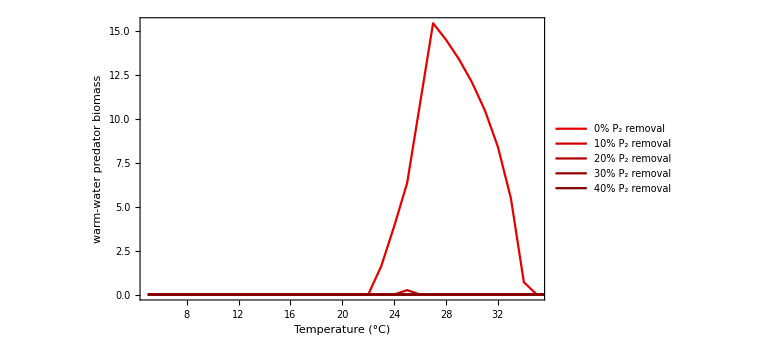

```mathematica
Clear[P2plot]
P2plot=ListLinePlot[{P2h0,P2h1,P2h2,P2h3,P2h4}, PlotRange->{{5,35},All}, Frame->True, FrameLabel->{{"warm-water predator biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"0% P_2 removal", "10% P_2 removal", "20% P_2 removal", "30% P_2 removal", "40% P_2 removal"},
PlotStyle -> {Darker[Red,0.1],Darker[Red,0.2],Darker[Red,0.3],Darker[Red,0.4],Darker[Red,0.5]}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

### C_1

```mathematica
Clear[bifMeanC1]
bifMeanC1=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->val/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,val,Chop[Mean[C1[Range[4000,5000]]]/.sol1,10^-2]}],{val,0,40,1},{hin,0,1,0.1}]],2];
```

```mathematica
(* Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
Clear[C1h0,C1h1,C1h2,C1h3,C1h4]
C1h0 =Take[bifMeanC1[[All,2;;3]],{1,Length[bifMeanC1],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the second h of each (i.e. h=0.1)*)
C1h1 =Take[bifMeanC1[[All,2;;3]],{2,Length[bifMeanC1],11}]; (*5 is h=0.4*)
C1h2 =Take[bifMeanC1[[All,2;;3]],{3,Length[bifMeanC1],11}]; (*5 is h=0.4*)
C1h3 =Take[bifMeanC1[[All,2;;3]],{4,Length[bifMeanC1],11}]; (*5 is h=0.4*)
C1h4 =Take[bifMeanC1[[All,2;;3]],{5,Length[bifMeanC1],11}]; (*5 is h=0.4*)
```

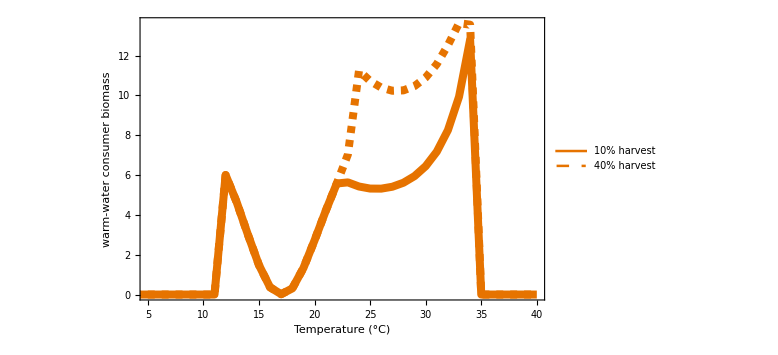

```mathematica
Clear[C1plot]
C1plotb=ListLinePlot[{C1h0,C1h4}, PlotRange->{{5,40},All}, Frame->True, FrameLabel->{{"warm-water consumer biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"10% harvest", "40% harvest"},
PlotStyle -> {{Thickness[0.01],Darker[Orange,0.1]},{Thickness[0.01],Dashed,Darker[Orange,0.1]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

### R_1

```mathematica
Clear[bifMeanR1]
bifMeanR1=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->val/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,val,Chop[Mean[R1[Range[4000,5000]]]/.sol1,10^-2]}],{val,5,40,1},{hin,0,1,0.1}]],2];
```

```mathematica
(* Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
Clear[R1h0,R1h1,R1h2,R1h3,Rh4]
R1h0 =Take[bifMeanR1[[All,2;;3]],{1,Length[bifMeanR1],11}] (*plot positions 2 and 3 (i.e. temperature and biomass) for the second h of each (i.e. h=0.1)*)
R1h1 =Take[bifMeanR1[[All,2;;3]],{2,Length[bifMeanR1],11}];
R1h2 =Take[bifMeanR1[[All,2;;3]],{3,Length[bifMeanR1],11}];
R1h3 =Take[bifMeanR1[[All,2;;3]],{4,Length[bifMeanR1],11}];
R1h4 =Take[bifMeanR1[[All,2;;3]],{5,Length[bifMeanR1],11}] (*5 is h=0.4*)
```

{{5,10.},{6,10.},{7,10.},{8,10.},{9,10.},{10,10.},{11,10.},{12,9.31012},{13,8.89328},{14,8.43412},{15,7.93507},{16,7.39065},{17,6.78494},{18,6.17002},{19,5.51866},{20,4.8688},{21,4.24275},{22,3.65831},{23,3.58482},{24,3.73596},{25,3.98839},{26,4.75871},{27,5.66918},{28,5.563},{29,5.47631},{30,5.41573},{31,5.39428},{32,5.43529},{33,5.58533},{34,5.95326},{35,10.},{36,10.},{37,10.},{38,10.},{39,10.},{40,10.}}

{{5,10.},{6,10.},{7,10.},{8,10.},{9,10.},{10,10.},{11,10.},{12,9.31054},{13,8.89328},{14,8.43412},{15,7.93507},{16,7.39065},{17,6.78494},{18,6.17002},{19,5.51866},{20,4.8688},{21,4.24275},{22,3.65831},{23,3.06592},{24,1.77804},{25,1.75637},{26,1.76759},{27,1.81251},{28,1.89846},{29,2.03821},{30,2.25017},{31,2.57072},{32,3.07532},{33,3.9431},{34,5.71672},{35,10.},{36,10.},{37,10.},{38,10.},{39,10.},{40,10.}}

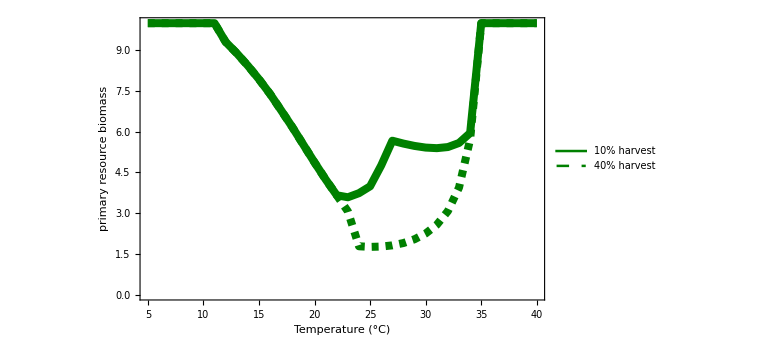

```mathematica
Clear[R1plot]
R1plot=ListLinePlot[{R1h0,R1h4}, PlotRange->{{5,40},All}, Frame->True, FrameLabel->{{"primary resource biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"10% harvest", "40% harvest"},
PlotStyle -> {{Thickness[0.01],Darker[Green,0.5]},{Thickness[0.01],Dashed, Darker[Green,0.5]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

### R_2

```mathematica
Clear[bifMeanR2]
bifMeanR2=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->val/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,val,Chop[Mean[R2[Range[4000,5000]]]/.sol1,10^-2]}],{val,5,40,1},{hin,0,1,0.1}]],2];
```

```mathematica
(* Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
Clear[R2h0,R2h4]
R2h0 =Take[bifMeanR2[[All,2;;3]],{2,Length[bifMeanR2],11}]; (*plot positions 2 and 3 (i.e. temperature and biomass) for the second h of each (i.e. h=0.1)*)
R2h4 =Take[bifMeanR2[[All,2;;3]],{5,Length[bifMeanR2],11}]; (*5 is h=0.4*)
```

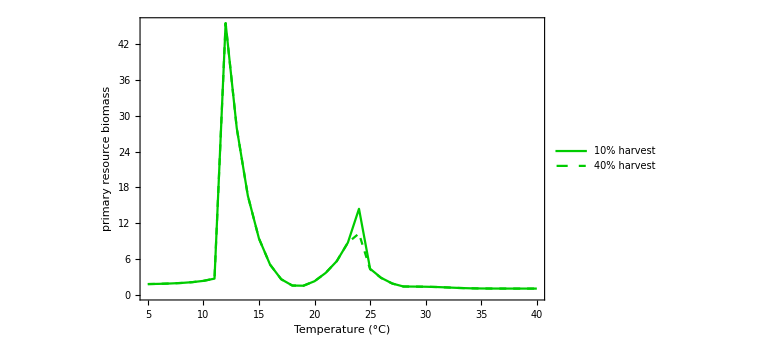

```mathematica
Clear[R2plot]
R2plot=ListLinePlot[{R2h0,R2h4}, PlotRange->{{5,40},All}, Frame->True, FrameLabel->{{"primary resource biomass", ""}, {"Temperature (°C)", ""}}, PlotLegends->{"10% harvest", "40% harvest"},
PlotStyle -> {Darker[Green,0.2],{Dashed, Darker[Green,0.2]}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

### All

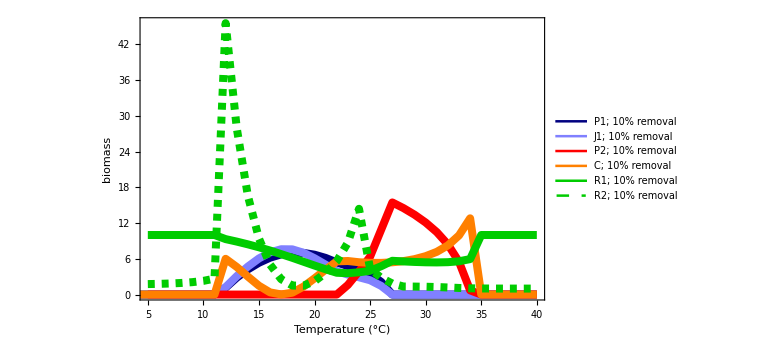

```mathematica
Clear[Allplot1]
Allplot1=ListLinePlot[{P1h0,J1h0,P2h0,C1h0,R1h0,R2h0}, PlotRange->{{5,40},All}, Frame->True, FrameLabel->{{"biomass",""},{"Temperature (°C)","all species; T_maxJ = 28°C"}}, 
PlotLegends->{"P1; 10% removal","J1; 10% removal", "P2; 10% removal", "C; 10% removal", "R1; 10% removal", "R2; 10% removal"},
PlotStyle -> {{Thickness[0.01],Darker[Blue,0.5]},{Thickness[0.01],Lighter[Blue,0.5]}, {Thickness[0.01],Red}, {Thickness[0.01], Orange}, {Thickness[0.01],Darker[Green,0.2]}, {Thickness[0.01],Darker[Green,0.2],Dashed}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

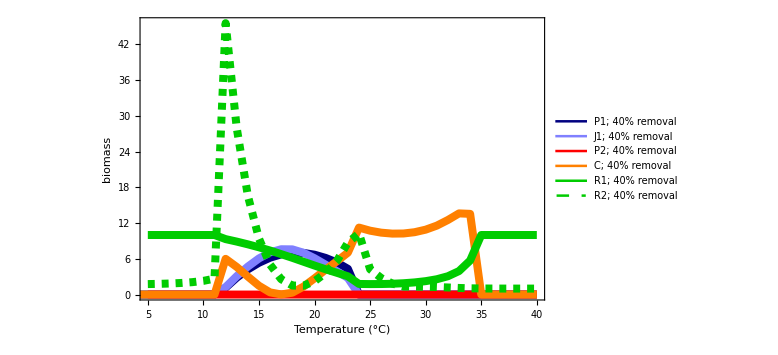

```mathematica
Clear[Allplot2]
Allplot2=ListLinePlot[{P1h4,J1h4,P2h4,C1h4,R1h4,R2h4}, PlotRange->{{5,40},All}, Frame->True, FrameLabel->{{"biomass",""},{"Temperature (°C)","all species; T_maxJ = 28°C"}}, 
PlotLegends->{"P1; 40% removal","J1; 40% removal", "P2; 40% removal", "C; 40% removal", "R1; 40% removal", "R2; 40% removal"},
PlotStyle -> {{Thickness[0.01],Darker[Blue,0.5]},{Thickness[0.01],Lighter[Blue,0.5]}, {Thickness[0.01],Red}, {Thickness[0.01], Orange}, {Thickness[0.01],Darker[Green,0.2]}, {Thickness[0.01],Darker[Green,0.2],Dashed}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

without R2

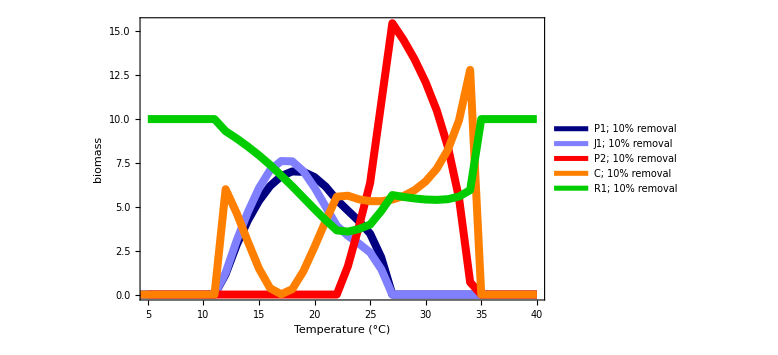

```mathematica
Clear[Allplot3]
Allplot3=ListLinePlot[{P1h0,J1h0,P2h0,C1h0,R1h0}, PlotRange->{{5,40},All}, Frame->True, FrameLabel->{{"biomass",""},{"Temperature (°C)","all species; T_maxJ = 28°C"}}, 
PlotLegends->{"P1; 10% removal","J1; 10% removal", "P2; 10% removal", "C; 10% removal", "R1; 10% removal"},
PlotStyle -> {{Thickness[0.01],Darker[Blue,0.5]},{Thickness[0.01],Lighter[Blue,0.5]}, {Thickness[0.01],Red}, {Thickness[0.01], Orange}, {Thickness[0.01],Darker[Green,0.2]}, {Thickness[0.01],Darker[Green,0.2],Dashed}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

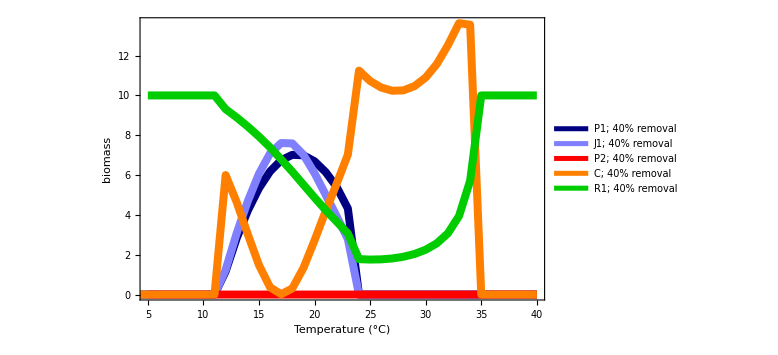

```mathematica
Clear[Allplot4]
Allplot4=ListLinePlot[{P1h4,J1h4,P2h4,C1h4,R1h4}, PlotRange->{{5,40},All}, Frame->True, FrameLabel->{{"biomass",""},{"Temperature (°C)","all species; T_maxJ = 28°C"}}, 
PlotLegends->{"P1; 40% removal","J1; 40% removal", "P2; 40% removal", "C; 40% removal", "R1; 40% removal"},
PlotStyle -> {{Thickness[0.01],Darker[Blue,0.5]},{Thickness[0.01],Lighter[Blue,0.5]}, {Thickness[0.01],Red}, {Thickness[0.01], Orange}, {Thickness[0.01],Darker[Green,0.2]}, {Thickness[0.01],Darker[Green,0.2],Dashed}}, ImageSize->Large, LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

## Cascades (log ratios )

### P_1

#### Bluegill as C1

with pred (h=0)

```mathematica
ratioP1p=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.h3->0/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[P1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

without pred (h=0.4)

```mathematica
ratioP1np=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.h3->0.4/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[P1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

dividing the second value of the first list (biomass with pred) by the second value of the second list (biomass without pred), then taking the log of that number
for “P1logratio” I tried adding 1 to the values so that we’d just get zeros for the indeterminate (divide by zero error) values.

```mathematica
P1logratio =Transpose[{ratioP1p[[All,1]],Log[ratioP1p[[All,2]]/ratioP1np[[All,2]]]}];
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

change Tmax4 & Topt (values taken from  Hasnain 2013 supplement)
b Yellow Perch :  Tmax4 = 35; Topt4 = 25 (28 & 23 C from FB4, respectively
c Golden Shiner : Tmax4 = 32; Topt4 = 25
d Black Crappie : Tmax4 = 34.9; Topt4 = 18
e Pumpkinseed : Tmax4 = 37.6; Topt4 = 25

#### Yellow Perch as C1

with pred (h=0)

```mathematica
ratioP1pb=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.Tmax4->35/.Topt4->25/.h3->0/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[P1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

without pred (h=0.4)

```mathematica
ratioP1npb=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.Tmax4->35/.Topt4->25/.h3->0.4/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[P1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

dividing the second value of the first list (biomass with pred) by the second value of the second list (biomass without pred), then taking the log of that number
for “P1logratio” I tried adding 1 to the values so that we’d just get zeros for the indeterminate (divide by zero error) values.

```mathematica
P1logratiob =Transpose[{ratioP1pb[[All,1]],Log[ratioP1pb[[All,2]]/ratioP1npb[[All,2]]]}];
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

change Tmax4 & Topt (values taken from  Hasnain 2013 supplement)
b Yellow Perch :  Tmax4 = 35; Topt4 = 25 (28 & 23 C from FB4, respectively
c Golden Shiner : Tmax4 = 32; Topt4 = 25
d Black Crappie : Tmax4 = 34.9; Topt4 = 18
e Pumpkinseed : Tmax4 = 37.6; Topt4 = 25

### J_1

#### Bluegill as C1

```mathematica
ratioJ1p=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.h3->0/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[J1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
ratioJ1np=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.h3->0.4/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[J1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
J1logratio=Transpose[{ratioJ1p[[All,1]],Log[ratioJ1p[[All,2]]/ratioJ1np[[All,2]]]}] ;
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

#### Yellow Perch as C1

```mathematica
ratioJ1pb=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.Tmax4->35/.Topt4->25/.h3->0/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[J1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
ratioJ1npb=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.Tmax4->35/.Topt4->25/.h3->0.4/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[J1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
J1logratiob=Transpose[{ratioJ1pb[[All,1]],Log[ratioJ1pb[[All,2]]/ratioJ1npb[[All,2]]]}] ;
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

### R_2

#### Bluegill as C1

p is with predator, np is no predator (no P2)

```mathematica
ratioC1p=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.h3->0/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[C1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
ratioC1np=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.h3->0.4/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[C1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
C1logratio =Transpose[{ratioC1p[[All,1]],Log[ratioC1p[[All,2]]/ratioC1np[[All,2]]]}] (*transpose is combining the first number for ratioC1p ([[All, 1]])and the quotient of the second numbers ([[All,2]]) of ratioC1p and ratioC1np*)
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{10,Indeterminate},{11,Indeterminate},{12,0.000906249},{13,1.29008×10^-13},{14,0.},{15,-7.77156×10^-16},{16,-7.0018×10^-7},{17,-0.00132104},{18,-3.94608×10^-6},{19,0.},{20,-1.93401×10^-13},{21,4.35207×10^-14},{22,-2.67297×10^-12},{23,-0.221887},{24,-0.728835},{25,-0.700646},{26,-0.670063},{27,-0.636851},{28,-0.602075},{29,-0.565325},{30,-0.52504},{31,-0.478131},{32,-0.416736},{33,-0.316265},{34,-0.0568067},{35,Indeterminate},{36,Indeterminate},{37,Indeterminate},{38,Indeterminate},{39,Indeterminate},{40,Indeterminate}}

#### Yellow Perch as C1

p is with predator, np is no predator (no P2)

```mathematica
ratioC1pb=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.Tmax4->35/.Topt4->25/.h3->0/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[C1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
ratioC1npb=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.Tmax4->35/.Topt4->25/.h3->0.4/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[C1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
C1logratiob=Transpose[{ratioC1pb[[All,1]],Log[ratioC1pb[[All,2]]/ratioC1npb[[All,2]]]}] (*transpose is combining the first number for ratioC1p ([[All, 1]])and the quotient of the second numbers ([[All,2]]) of ratioC1p and ratioC1np*)
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{10,0.},{11,9.52571×10^-14},{12,-7.77156×10^-16},{13,-6.27276×10^-14},{14,-5.35127×10^-14},{15,-4.70735×10^-14},{16,-1.79856×10^-14},{17,-3.06422×10^-14},{18,1.11022×10^-15},{19,-1.09357×10^-13},{20,-0.00566441},{21,-0.110748},{22,-0.221273},{23,-0.352195},{24,-0.665327},{25,-0.668965},{26,-0.670102},{27,-0.668404},{28,-0.663759},{29,-0.654726},{30,-0.639623},{31,-0.612248},{32,-0.548433},{33,-0.309937},{34,Indeterminate},{35,Indeterminate},{36,Indeterminate},{37,Indeterminate},{38,Indeterminate},{39,Indeterminate},{40,Indeterminate}}

### R_1

#### Bluegill as C1

```mathematica
ratioR1p=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.h3->0/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[R1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
ratioR1np=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.h3->0.4/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[R1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
R1logratio=Transpose[{ratioR1p[[All,1]],Log[(1+ratioR1p[[All,2]])/(1+ratioR1np[[All,2]])]}] ;
```

#### Yellow Perch as C1

```mathematica
ratioR1pb=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.Tmax4->35/.Topt4->25/.h3->0/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[R1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
ratioR1npb=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.Tmax4->35/.Topt4->25/.h3->0.4/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[Mean[R1[Range[4000,5000]]]/.sol,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
R1logratiob=Transpose[{ratioR1pb[[All,1]],Log[(1+ratioR1pb[[All,2]])/(1+ratioR1npb[[All,2]])]}] ;
```

### All

Here, P1, J, and R1 have Log(Np2+/Np2-) close to zero because their biomass values are very similar (if not  exactly the same) so Log(1)=0. Whereas C biomass is zero until 22C.

#### Bluegill as consumer

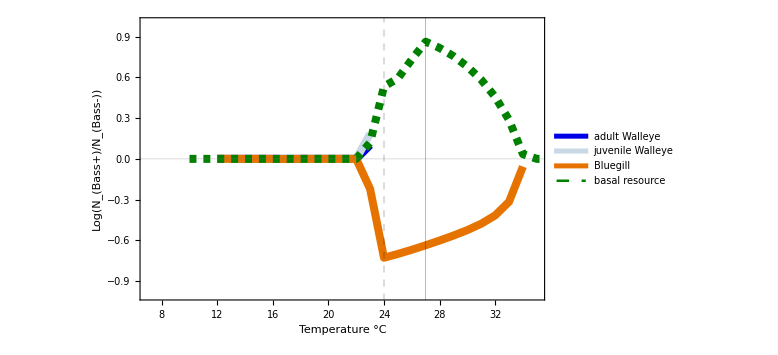

```mathematica
Show[
ListLinePlot[P1logratio, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Blue,0.1]},PlotLegends->{"adult Walleye"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],ListLinePlot[J1logratio, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[LightBlue,0.1]},PlotLegends->{"juvenile Walleye"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],
ListLinePlot[C1logratio, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Orange,0.1]},PlotLegends->{"Bluegill"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],
ListLinePlot[R1logratio, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Green, 0.5],Dashed},PlotLegends->{"basal resource"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],
PlotRange->{{7,35},{-1,1}}, Frame->True, FrameLabel->{"Temperature °C","Log(N_(Bass+)/N_(Bass-))"}, ImageSize->Large, LabelStyle->Directive[FontSize->20, FontFamily->"Arial", FontColor->Black
], Frame->True, GridLines->{{{24,Directive[Thickness->.005,Dashed,Black]},{27,Directive[Thickness->.005,Black]}},{0}}, Axes->False
]
```

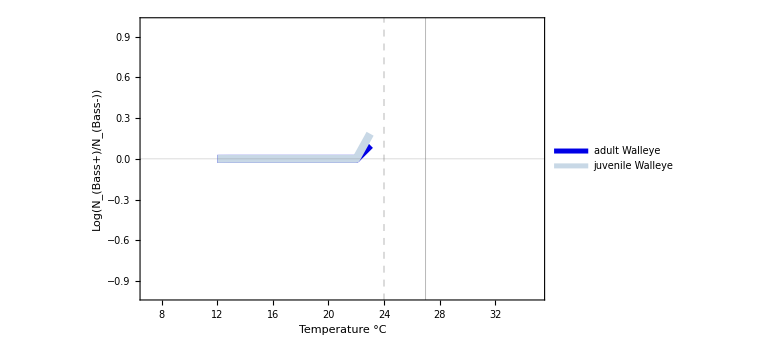

```mathematica
Show[
ListLinePlot[P1logratio, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Blue,0.1]},PlotLegends->{"adult Walleye"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],ListLinePlot[J1logratio, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[LightBlue,0.1]},PlotLegends->{"juvenile Walleye"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],
PlotRange->{{7,35},{-1,1}}, Frame->True, FrameLabel->{"Temperature °C","Log(N_(Bass+)/N_(Bass-))"}, ImageSize->Large, LabelStyle->Directive[FontSize->20, FontFamily->"Arial", FontColor->Black
], Frame->True, GridLines->{{{24,Directive[Thickness->.005,Dashed,Black]},{27,Directive[Thickness->.005,Black]}},{0}}, Axes->False
]
```

#### Yellow Perch as consumer

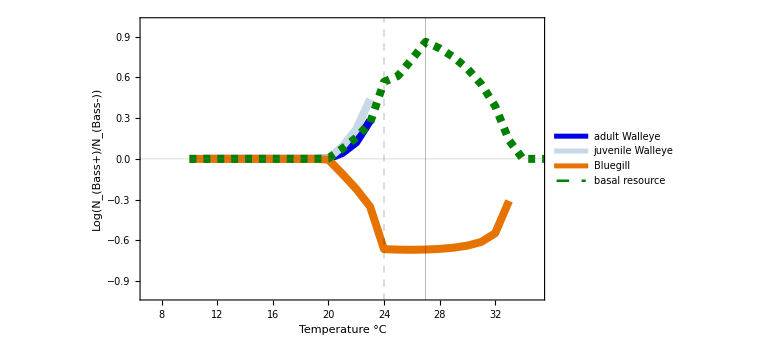

```mathematica
Show[
ListLinePlot[P1logratiob, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Blue,0.1]},PlotLegends->{"adult Walleye"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],ListLinePlot[J1logratiob, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[LightBlue,0.1]},PlotLegends->{"juvenile Walleye"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],
ListLinePlot[C1logratiob, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Orange,0.1]},PlotLegends->{"Bluegill"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],
ListLinePlot[R1logratiob, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Green, 0.5],Dashed},PlotLegends->{"basal resource"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],
PlotRange->{{7,35},{-1,1}}, Frame->True, FrameLabel->{"Temperature °C","Log(N_(Bass+)/N_(Bass-))"}, ImageSize->Large, LabelStyle->Directive[FontSize->20, FontFamily->"Arial", FontColor->Black
], Frame->True, GridLines->{{{24,Directive[Thickness->.005,Dashed,Black]},{27,Directive[Thickness->.005,Black]}},{0}}, Axes->False
]
```

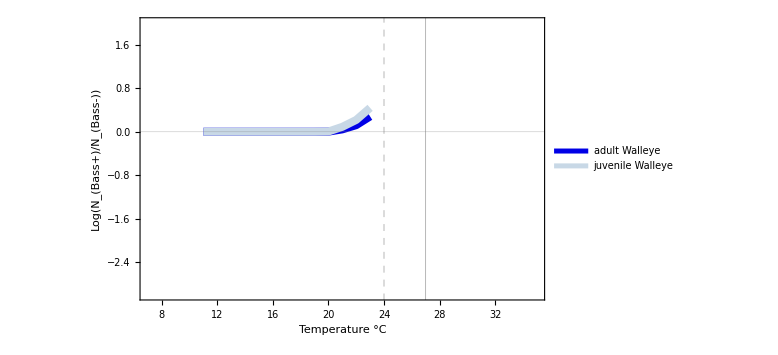

```mathematica
Show[
ListLinePlot[P1logratiob, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Blue,0.1]},PlotLegends->{"adult Walleye"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],ListLinePlot[J1logratiob, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[LightBlue,0.1]},PlotLegends->{"juvenile Walleye"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],
PlotRange->{{7,35},{-3,2}}, Frame->True, FrameLabel->{"Temperature °C","Log(N_(Bass+)/N_(Bass-))"}, ImageSize->Large, LabelStyle->Directive[FontSize->20, FontFamily->"Arial", FontColor->Black
], Frame->True, GridLines->{{{24,Directive[Thickness->.005,Dashed,Black]},{27,Directive[Thickness->.005,Black]}},{0}}, Axes->False
]
```

## Cascades (log flux ratios)

### P_1

#### Bluegill as C1

with pred (h=0)

```mathematica
fratioP1p=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.h3->0/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[awa1*Piecewise[{{Exp[-((val-Topt1)/(2 σ))^2],val<Topt1},{1-((val-(Topt1))/((Topt1)-Tmax1))^2,Tmax1>val≥Topt1},{0,val≥Tmax1}}]Mean[C1[Range[4000,5000]]]Mean[P1[Range[4000,5000]]]/.sol/.params,10^-2]}],{val,10,40,1}]],1];
```

without pred (h=0.4)

```mathematica
fratioP1np=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.h3->0.4/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[awa1*Piecewise[{{Exp[-((val-Topt1)/(2 σ))^2],val<Topt1},{1-((val-(Topt1))/((Topt1)-Tmax1))^2,Tmax1>val≥Topt1},{0,val≥Tmax1}}]Mean[C1[Range[4000,5000]]]Mean[P1[Range[4000,5000]]]/.sol/.params,10^-2]}],{val,10,40,1}]],1];
```

dividing the second value of the first list (biomass with pred) by the second value of the second list (biomass without pred), then taking the log of that number
for “P1logratio” I tried adding 1 to the values so that we’d just get zeros for the indeterminate (divide by zero error) values.

```mathematica
P1logfratio=Transpose[{fratioP1p[[All,1]],Log[fratioP1p[[All,2]]/fratioP1np[[All,2]]]}];
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

#### Yellow Perch as C1

with pred (h=0)

```mathematica
fratioP1pb=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.Tmax4->35/.Topt4->25/.h3->0/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[awa1*Piecewise[{{Exp[-((val-Topt1)/(2 σ))^2],val<Topt1},{1-((val-(Topt1))/((Topt1)-Tmax1))^2,Tmax1>val≥Topt1},{0,val≥Tmax1}}]Mean[C1[Range[4000,5000]]]Mean[P1[Range[4000,5000]]]/.sol/.params,10^-2]}],{val,10,40,1}]],1];
```

without pred (h=0.4)

```mathematica
fratioP1npb=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.Tmax4->35/.Topt4->25/.h3->0.4/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[awa1*Piecewise[{{Exp[-((val-Topt1)/(2 σ))^2],val<Topt1},{1-((val-(Topt1))/((Topt1)-Tmax1))^2,Tmax1>val≥Topt1},{0,val≥Tmax1}}]Mean[C1[Range[4000,5000]]]Mean[P1[Range[4000,5000]]]/.sol/.params,10^-2]}],{val,10,40,1}]],1];
```

dividing the second value of the first list (biomass with pred) by the second value of the second list (biomass without pred), then taking the log of that number
for “P1logratio” I tried adding 1 to the values so that we’d just get zeros for the indeterminate (divide by zero error) values.

```mathematica
P1logfratiob=Transpose[{fratioP1pb[[All,1]],Log[fratioP1pb[[All,2]]/fratioP1npb[[All,2]]]}];
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

### J_1

#### Bluegill as C1

```mathematica
fratioJ1p=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.h3->0/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[aj1*Piecewise[{{Exp[-((val-Topt2)/(2 σ))^2],val<Topt2},{1-((val-(Topt2))/((Topt2)-Tmax2))^2,Tmax2>val≥Topt2},{0,Tin≥Tmax2}}]Mean[R1[Range[4000,5000]]]Mean[J1[Range[4000,5000]]]/.sol/.params,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
fratioJ1np=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.h3->0.4/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[aj1*Piecewise[{{Exp[-((val-Topt2)/(2 σ))^2],val<Topt2},{1-((val-(Topt2))/((Topt2)-Tmax2))^2,Tmax2>val≥Topt2},{0,Tin≥Tmax2}}]Mean[R1[Range[4000,5000]]]Mean[J1[Range[4000,5000]]]/.sol/.params,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
J1logfratio=Transpose[{fratioJ1p[[All,1]],Log[fratioJ1p[[All,2]]/fratioJ1np[[All,2]]]}] ;
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

#### Yellow Perch as C1

```mathematica
fratioJ1pb=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.Tmax4->35/.Topt4->25/.h3->0/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[aj1*Piecewise[{{Exp[-((val-Topt2)/(2 σ))^2],val<Topt2},{1-((val-(Topt2))/((Topt2)-Tmax2))^2,Tmax2>val≥Topt2},{0,Tin≥Tmax2}}]Mean[R1[Range[4000,5000]]]Mean[J1[Range[4000,5000]]]/.sol/.params,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
fratioJ1npb=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.Tmax4->35/.Topt4->25/.h3->0.4/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[aj1*Piecewise[{{Exp[-((val-Topt2)/(2 σ))^2],val<Topt2},{1-((val-(Topt2))/((Topt2)-Tmax2))^2,Tmax2>val≥Topt2},{0,Tin≥Tmax2}}]Mean[R1[Range[4000,5000]]]Mean[J1[Range[4000,5000]]]/.sol/.params,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
J1logfratiob=Transpose[{fratioJ1pb[[All,1]],Log[fratioJ1pb[[All,2]]/fratioJ1npb[[All,2]]]}] ;
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

### R_2

p is with predator, np is no predator (no P2)

#### Bluegill as C1

```mathematica
fratioC1p=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.h3->0/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[ac1*Piecewise[{{Exp[-((val-Topt4)/(2 σ))^2],val<Topt4},{1-((val-(Topt4))/((Topt4)-Tmax4))^2,Tmax4>val≥Topt4},{0,val≥Tmax4}}]Mean[R1[Range[4000,5000]]]Mean[C1[Range[4000,5000]]]/.sol/.params,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
fratioC1np=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.h->0.4/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[ac1*Piecewise[{{Exp[-((val-Topt4)/(2 σ))^2],val<Topt4},{1-((val-(Topt4))/((Topt4)-Tmax4))^2,Tmax4>val≥Topt4},{0,val≥Tmax4}}]Mean[R1[Range[4000,5000]]]Mean[C1[Range[4000,5000]]]/.sol/.params,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
C1logfratio =Transpose[{fratioC1p[[All,1]],Log[fratioC1p[[All,2]]/fratioC1np[[All,2]]]}] ;(*transpose is combining the first number for ratioC1p ([[All, 1]])and the quotient of the second numbers ([[All,2]]) of ratioC1p and ratioC1np*)
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

#### Yellow Perch as C1

```mathematica
fratioC1pb=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.Tmax4->35/.Topt4->25/.h3->0/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[ac1*Piecewise[{{Exp[-((val-Topt4)/(2 σ))^2],val<Topt4},{1-((val-(Topt4))/((Topt4)-Tmax4))^2,Tmax4>val≥Topt4},{0,val≥Tmax4}}]Mean[R1[Range[4000,5000]]]Mean[C1[Range[4000,5000]]]/.sol/.params,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
fratioC1npb=Flatten[Module[{sol},
Table[sol=NDSolve[{PdSystem[{1,1,1,1,1 ,1}]/.T->val/.Tmax4->35/.Topt4->25/.h->0.4/.rates/.params},{R1,C1,J1,P1,P2,R2},{t,4000,5000},AccuracyGoal->30, PrecisionGoal->10, MaxStepSize->0.1,MaxSteps->100000];
Thread[{val,Chop[ac1*Piecewise[{{Exp[-((val-Topt4)/(2 σ))^2],val<Topt4},{1-((val-(Topt4))/((Topt4)-Tmax4))^2,Tmax4>val≥Topt4},{0,val≥Tmax4}}]Mean[R1[Range[4000,5000]]]Mean[C1[Range[4000,5000]]]/.sol/.params,10^-2]}],{val,10,40,1}]],1];
```

```mathematica
C1logfratiob=Transpose[{fratioC1pb[[All,1]],Log[fratioC1pb[[All,2]]/fratioC1npb[[All,2]]]}] ;(*transpose is combining the first number for ratioC1p ([[All, 1]])and the quotient of the second numbers ([[All,2]]) of ratioC1p and ratioC1np*)
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

### All

#### Bluegill as C1

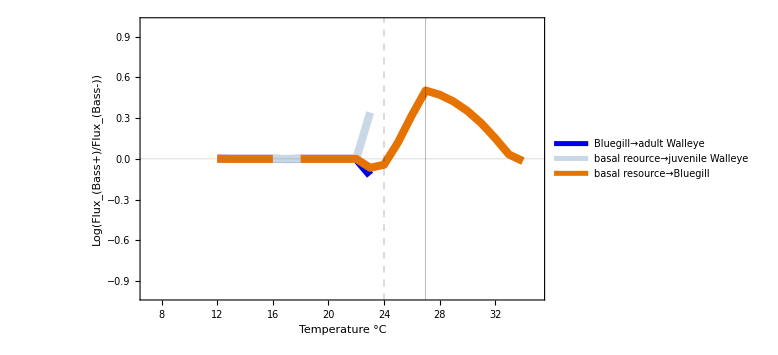

```mathematica
Show[
ListLinePlot[P1logfratio, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Blue,0.1]},PlotLegends->{"Bluegill→adult Walleye"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],
ListLinePlot[J1logfratio, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[LightBlue,0.1]},PlotLegends->{"basal reource→juvenile Walleye"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],
ListLinePlot[C1logfratio, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Orange,0.1]},PlotLegends->{"basal resource→Bluegill"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],
PlotRange->{{7,35},{-1,1}}, Frame->True, FrameLabel->{"Temperature °C","Log(Flux_(Bass+)/Flux_(Bass-))"}, ImageSize->Large, LabelStyle->Directive[FontSize->20, FontFamily->"Arial", FontColor->Black], Frame->True , GridLines->{{{24,Directive[Thickness->.005, Dashed,Black]},{27,Directive[Thickness->.005,Black]}},{0}} , Axes->False
]
```

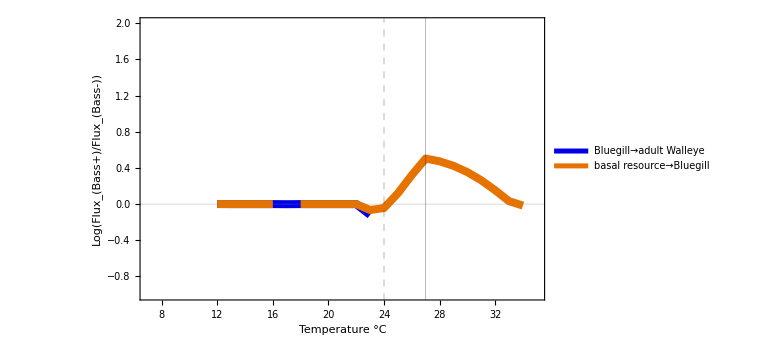

```mathematica
Show[
ListLinePlot[P1logfratio, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Blue,0.1]},PlotLegends->{"Bluegill→adult Walleye"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],
ListLinePlot[C1logfratio, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Orange,0.1]},PlotLegends->{"basal resource→Bluegill"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],
PlotRange->{{7,35},{-1,2}}, Frame->True, FrameLabel->{"Temperature °C","Log(Flux_(Bass+)/Flux_(Bass-))"}, ImageSize->Large, LabelStyle->Directive[FontSize->20, FontFamily->"Arial", FontColor->Black], Frame->True , GridLines->{{{24,Directive[Thickness->.005, Dashed,Black]},{27,Directive[Thickness->.005,Black]}},{0}} , Axes->False
]
```

#### Yellow Perch as C1

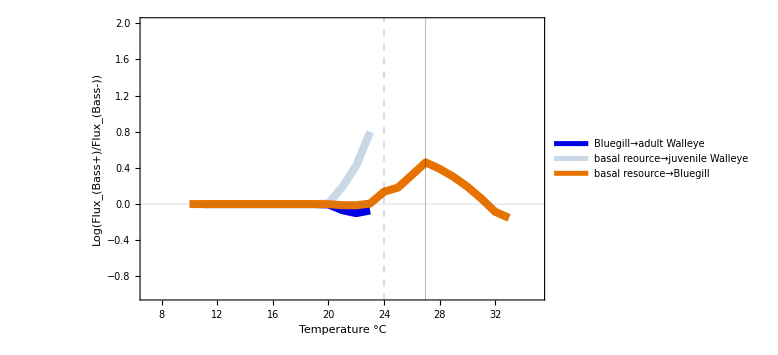

```mathematica
Show[
ListLinePlot[P1logfratiob, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Blue,0.1]},PlotLegends->{"Bluegill→adult Walleye"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],
ListLinePlot[J1logfratiob, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[LightBlue,0.1]},PlotLegends->{"basal reource→juvenile Walleye"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],
ListLinePlot[C1logfratiob, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Orange,0.1]},PlotLegends->{"basal resource→Bluegill"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],
PlotRange->{{7,35},{-1,2}}, Frame->True, FrameLabel->{"Temperature °C","Log(Flux_(Bass+)/Flux_(Bass-))"}, ImageSize->Large, LabelStyle->Directive[FontSize->20, FontFamily->"Arial", FontColor->Black], Frame->True , GridLines->{{{24,Directive[Thickness->.005, Dashed,Black]},{27,Directive[Thickness->.005,Black]}},{0}} , Axes->False
]
```

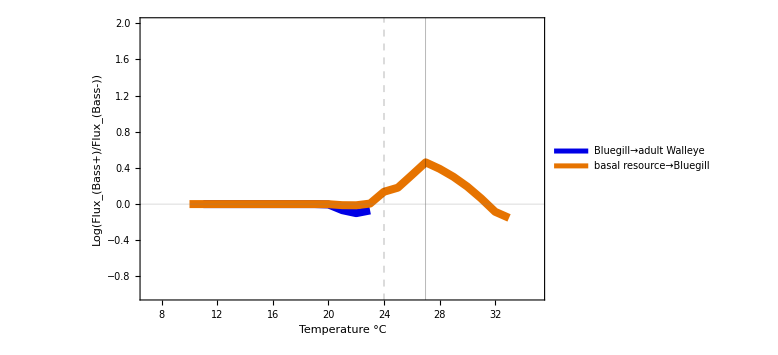

```mathematica
Show[
ListLinePlot[P1logfratiob, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Blue,0.1]},PlotLegends->{"Bluegill→adult Walleye"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],
ListLinePlot[C1logfratiob, PlotRange->All, PlotStyle->{Thickness[0.01],Darker[Orange,0.1]},PlotLegends->{"basal resource→Bluegill"},LabelStyle->Directive[FontSize->20, FontFamily->"Arial"]],
PlotRange->{{7,35},{-1,2}}, Frame->True, FrameLabel->{"Temperature °C","Log(Flux_(Bass+)/Flux_(Bass-))"}, ImageSize->Large, LabelStyle->Directive[FontSize->20, FontFamily->"Arial", FontColor->Black], Frame->True , GridLines->{{{24,Directive[Thickness->.005, Dashed,Black]},{27,Directive[Thickness->.005,Black]}},{0}} , Axes->False
]
```

## P_1 Extinction Temperature

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[ExtMeanP1]
ExtMeanP1=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.ap2j1->ap2j1in/.T->val/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{ap2j1in,hin,val,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{ap2j1in,0.0,0.04,0.01},{val,21,35,1},{hin,0,0.5,0.1}]],3];
(*Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
```

```mathematica
ExtMeanP1;
```

Below is exporting the data for the heat map so that I don’t have to run the long code every time. If ANYTHING changes above, the code will have to be re-run...note that this data is called ext3. the other versions we’ve been using are ext2 and ext1

```mathematica
Export["ext3.csv",ExtMeanP1,"Table"];
```

```mathematica
Clear[data1]
data1=Import["ext3.csv", "Table"];
```

```mathematica
(*This is for the line plot...Here the code removes cases that correspond to each a22 value (was Tmax value 28-35)*)
P1se1 =Drop[Cases[data1,{0.00,_,_,_}],None,1];
P1se2 =Drop[Cases[data1,{0.01,_,_,_}],None,1];
P1se3 =Drop[Cases[data1,{0.02,_,_,_}],None,1];
P1se4 =Drop[Cases[data1,{0.03,_,_,_}],None,1];
P1se5 =Drop[Cases[data1,{0.04,_,_,_}],None,1];
```

```mathematica
(*Here the code should be extracting the data for the first case where density equals 0*)
P1ext1= Take[Table[FirstCase[P1se1,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext2= Take[Table[FirstCase[P1se2,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext3= Take[Table[FirstCase[P1se3,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext4= Take[Table[FirstCase[P1se4,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext5= Take[Table[FirstCase[P1se5,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
```

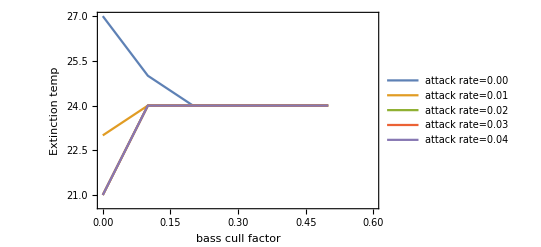

```mathematica
(*This is the line version of everything*)
P1plotA=ListLinePlot[{P1ext1,P1ext2,P1ext3,P1ext4,P1ext5}, PlotRange->{{0,0.6},All}, Frame->True, FrameLabel->{{"Extinction temp", ""}, {"bass cull factor", "(a) Cool-water predator"}}, PlotLegends->{"attack rate=0.00", "attack rate=0.01", "attack rate=0.02", "attack rate=0.03", "attack rate=0.04"}, LabelStyle->Directive[Medium]]
```

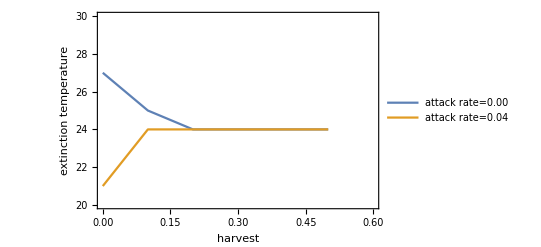

```mathematica
(*This is the line version of everything - condensed*) (*also, this is for cool-water predator when intermediate consumer is warm-water...used in MS*)
P1plotB=ListLinePlot[{P1ext1,P1ext5}, PlotRange->{{0,0.6},{20,30}}, Frame->True, FrameLabel->{{"extinction temperature", ""}, {"harvest", ""}}, PlotLegends->{"attack rate=0.00", "attack rate=0.04"},LabelStyle->Directive[Bold, Medium]]
```

the numbers refer to the bass attack rate on juvenile walleye (0.0-0.04)

```mathematica
(*This is where you start the heat map plot*)
P1x1 =Cases[data1,{0.00,_,_,_}];
P1x2 =Cases[data1,{0.01,_,_,_}];
P1x3 =Cases[data1,{0.02,_,_,_}];
P1x4 =Cases[data1,{0.03,_,_,_}];
P1x5 =Cases[data1,{0.04,_,_,_}];
```

Below is where you get the extinction temps for each attack rate (bass on juvenile); 0.0-0.04. The second set of brackets is for the bass removal rates (0 to 5 in increments of 0.1 - I (LJ) changed it from 0.01 to 0.1 to make it faster. The code is pulling the temperature at which the outcome goes to zero; showing all three columns of all combinations of attack rate and harvest.

```mathematica
P1T1= Take[Table[FirstCase[P1x1,{0.00,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T2= Take[Table[FirstCase[P1x2,{0.01,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T3= Take[Table[FirstCase[P1x3,{0.02,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T4= Take[Table[FirstCase[P1x4,{0.03,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T5= Take[Table[FirstCase[P1x5,{0.04,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
```

```mathematica
(*Here I join into one list on data*)
extdata1 = Join[P1T1,P1T2,P1T3,P1T4,P1T5];
Max[extdata1[[All,3]]]
Min[extdata1[[All,3]]]
```

27

21

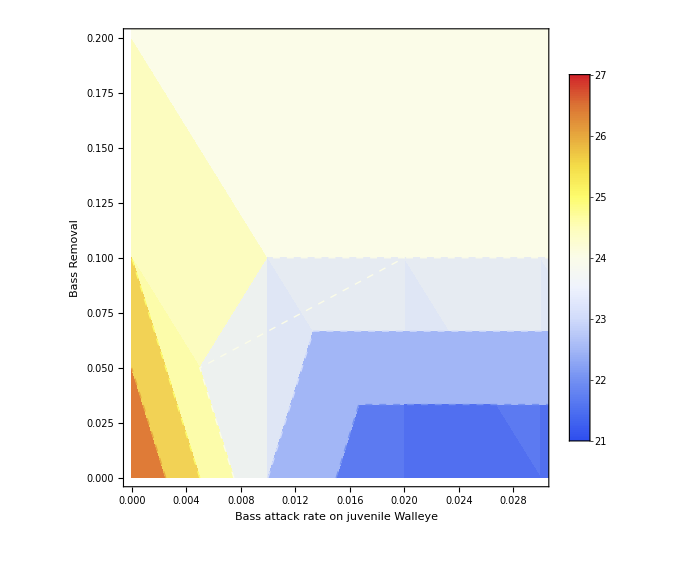

```mathematica
Clear[plot1] (*same plot as above, just different axes*)
plot1 = ListDensityPlot[extdata1, 
Mesh->5,FrameLabel->{{"Bass Removal"},{"Bass attack rate on juvenile Walleye"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->{{0,0.03},{0,0.2}},
PlotLegends-> BarLegend[{"TemperatureMap",{21,27}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial", FontColor->Black]]
```

## P_1 Extinction Temperature - heat maps (sensitivity to various params)

### biomass, P2 harvest, temp

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1]
biomP1=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->val/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,val,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{val,15,35,1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1[[All,3]],Except[Infinity|Indeterminate]] (*the "Max...[All, 3]]..." means the max value in the 3rd column (biomass value) for all rows*)
Min@Cases[biomP1[[All,3]],_?NumberQ]
```

7.01662

0

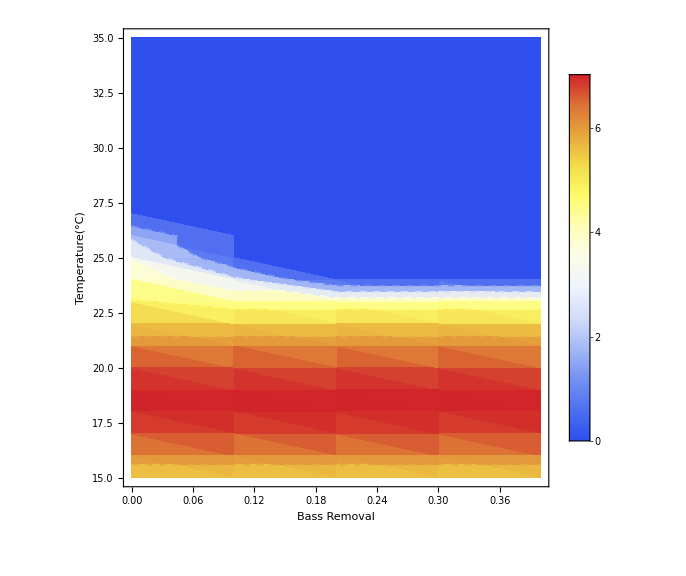

```mathematica
(*not sure if this plot even makes sense (like how I made it)...also, axes are wrong*)
Clear[plot4]
plot4 = ListDensityPlot[biomP1, 
Mesh->5,FrameLabel->{{"Temperature(°C)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,7.02}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

### biomass, P2 harvest, r1/r2/K1/K2

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1a1]
biomP1a1=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.r1->r1in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,r1in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{r1in,0.0,10,0.1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1a1[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1a1[[All,3]],_?NumberQ]]
```

3.47279

0

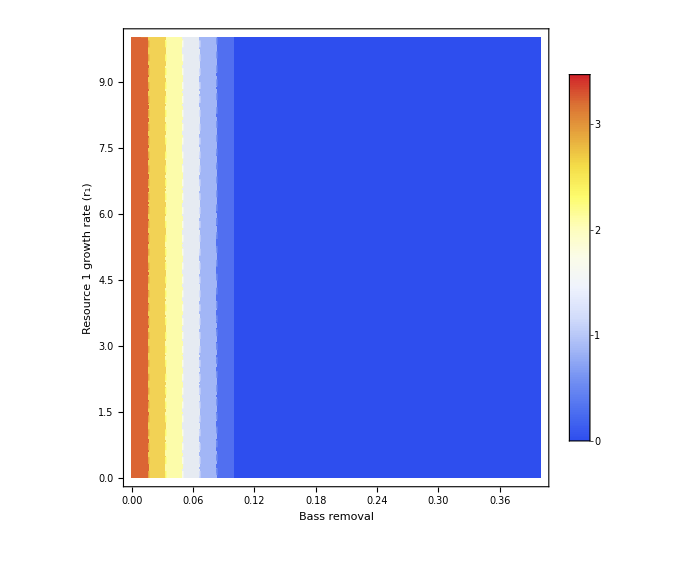

```mathematica
(*not sure if this plot even makes sense (like how I made it)...also, axes are wrong*)
Clear[plot2a]
plot2a = ListDensityPlot[biomP1a1, 
Mesh->5,FrameLabel->{{"Resource 1 growth rate (r_1)"},{"Bass removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,3.47}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
Clear[biomP1a2]
biomP1a2=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.r2->r2in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,r2in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{r2in,0.0,10,0.1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1a2[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1a2[[All,3]],_?NumberQ]]
```

3.47279

0

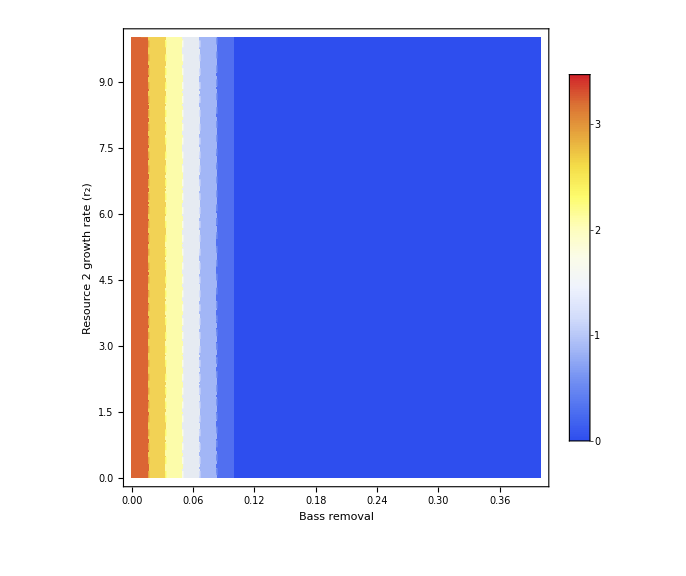

```mathematica
(*not sure if this plot even makes sense (like how I made it)...also, axes are wrong*)
Clear[plot2b]
plot2b = ListDensityPlot[biomP1a2, 
Mesh->5,FrameLabel->{{"Resource 2 growth rate (r_2)"},{"Bass removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,3.47}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1a3]
biomP1a3=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.K1->K1in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,K1in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{K1in,5,20,1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1a3[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1a3[[All,3]],_?NumberQ]]
```

6.17892

0

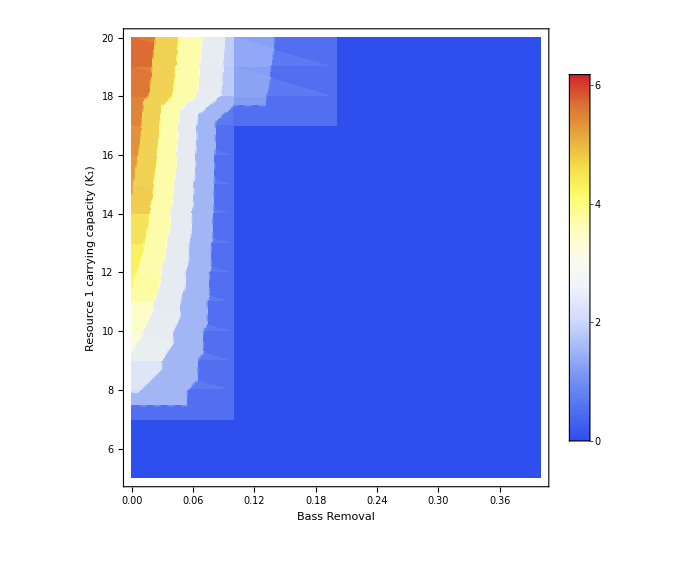

```mathematica
Clear[plot3a]
plot3a = ListDensityPlot[biomP1a3, 
Mesh->5,FrameLabel->{{"Resource 1 carrying capacity (K_1)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,6.18}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1a4]
biomP1a4=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.K2->K2in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,K2in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{K2in,5,20,1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1a4[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1a4[[All,3]],_?NumberQ]]
```

4.34024

0

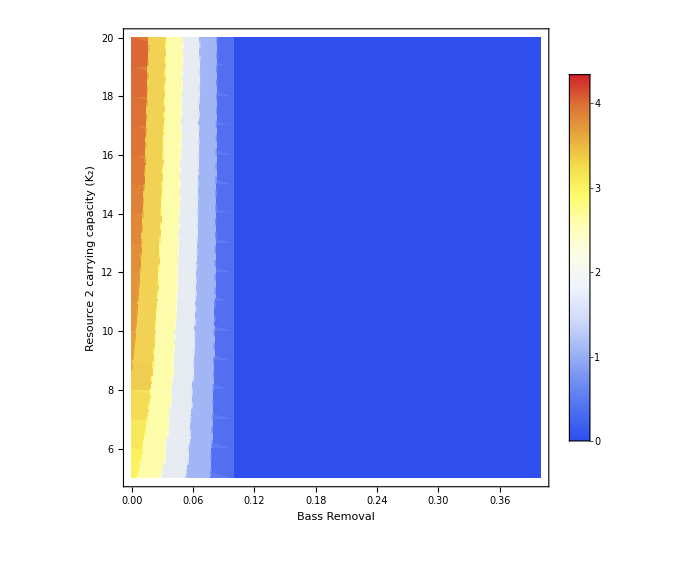

```mathematica
Clear[plot3b]
plot3b = ListDensityPlot[biomP1a4, 
Mesh->5,FrameLabel->{{"Resource 2 carrying capacity (K_2)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,4.34}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

### biomass, P2 harvest, a

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b1]
biomP1b1=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.ac1->ac1in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,ac1in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{ac1in,0.0,0.1,0.01}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

The below is getting the maximum and minimum biomass estimates to set the temp colour range in the plot

```mathematica
Max@Cases[biomP1b1[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b1[[All,3]],_?NumberQ]]
```

6.7022

0

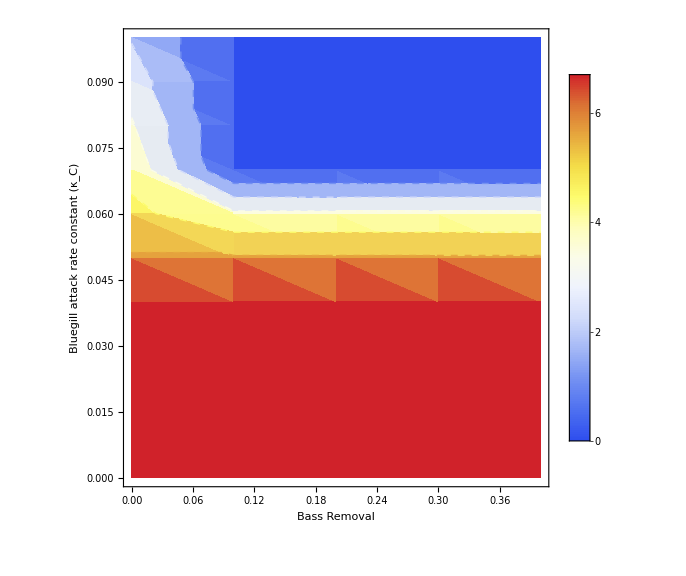

```mathematica
(*not sure if this plot even makes sense (like how I made it)...also, axes are wrong*)
Clear[plot5]
plot5 = ListDensityPlot[biomP1b1, 
Mesh->5,FrameLabel->{{"Bluegill attack rate constant (κ_C)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,6.70}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b2]
biomP1b2=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.aj1->aj1in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,aj1in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{aj1in,0.0,0.1,0.01}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1b2[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b2[[All,3]],_?NumberQ]]
```

3.82136

0

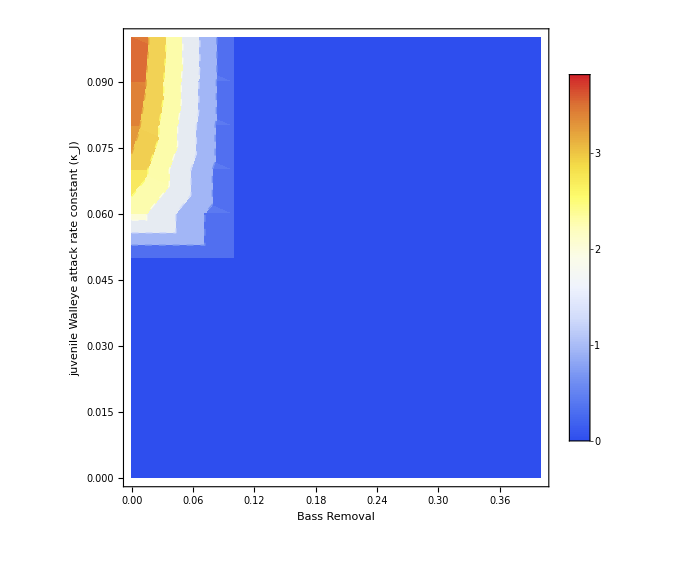

```mathematica
(*not sure if this plot even makes sense (like how I made it)...also, axes are wrong*)
Clear[plot6]
plot6 = ListDensityPlot[biomP1b2, 
Mesh->5,FrameLabel->{{"juvenile Walleye attack rate constant (κ_J)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,3.82}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b3]
biomP1b3=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.ap1c1->ap1c1in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,ap1c1in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{ap1c1in,0.0,0.1,0.01}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1b3[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b3[[All,3]],_?NumberQ]]
```

6.7022

0

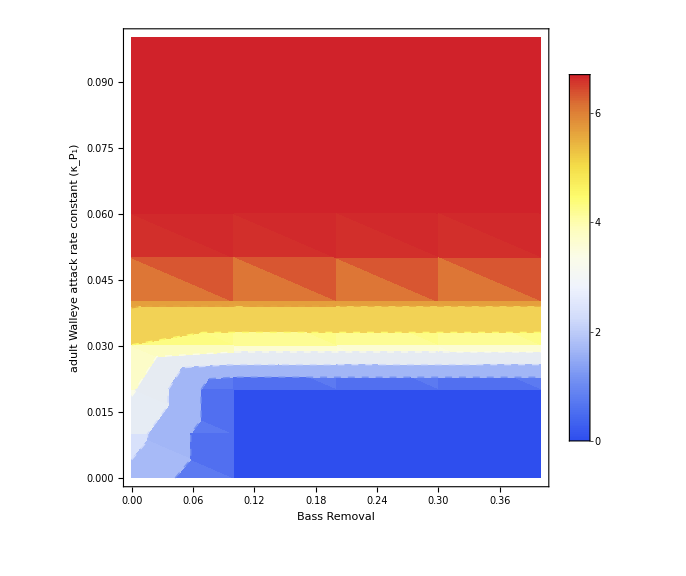

```mathematica
(*not sure if this plot even makes sense (like how I made it)...also, axes are wrong*)
Clear[plot7]
plot7 = ListDensityPlot[biomP1b3, 
Mesh->5,FrameLabel->{{"adult Walleye attack rate constant (κ_P_1)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,6.70}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b4]
biomP1b4=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.ap1r2->ap1r2in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,ap1r2in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{ap1r2in,0.0,0.1,0.001}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1b4[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b4[[All,3]],_?NumberQ]]
```

3.47279

0

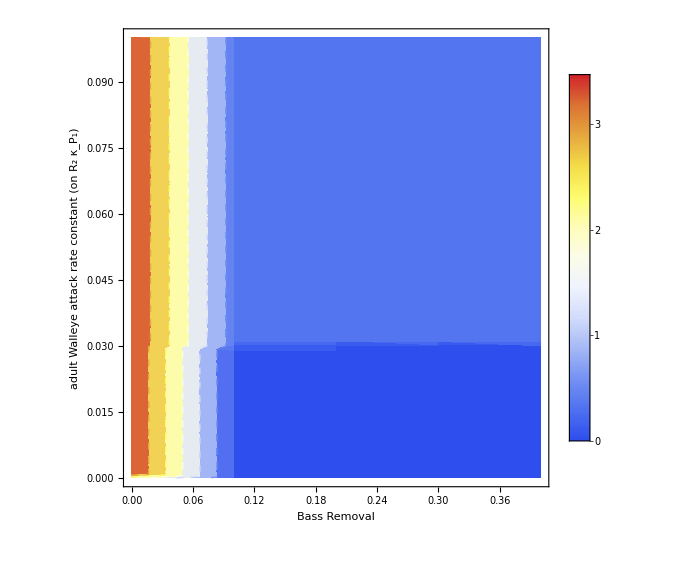

```mathematica
(*not sure if this plot even makes sense (like how I made it)...also, axes are wrong*)
Clear[plot7b]
plot7b = ListDensityPlot[biomP1b4, 
Mesh->5,FrameLabel->{{"adult Walleye attack rate constant (on R_2 κ_P_1)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,3.47}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1b5]
biomP1b5=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.ap2c1->ap2c1in/.h->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,ap2c1in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{ap2c1in,0.0,0.1,0.01}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1b5[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1b5[[All,3]],_?NumberQ]]
```

5.13951

0

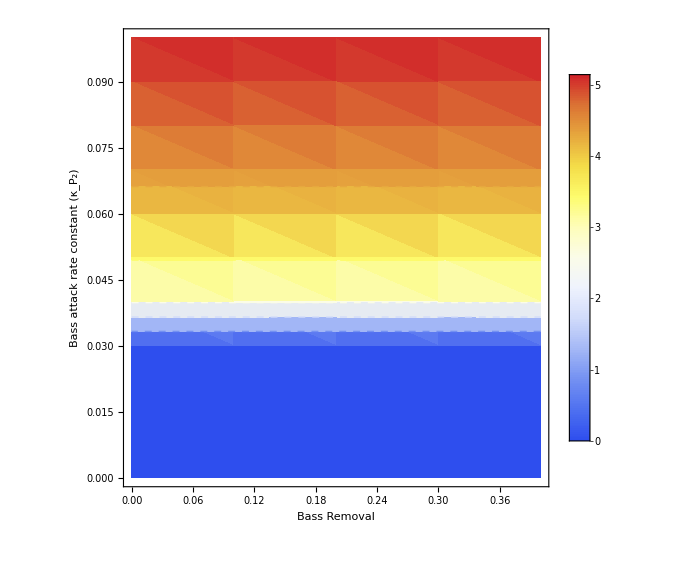

```mathematica
Clear[plot8]
plot8 = ListDensityPlot[biomP1b5, 
Mesh->5,FrameLabel->{{"Bass attack rate constant (κ_P_2)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,5.14}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

### biomass, P2 harvest, m

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1c1]
biomP1c1=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.mp1->mp1/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,mp1in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{mp1in,0.0,0.01,0.001}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1c1[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1c1[[All,3]],_?NumberQ]]
```

3.47279

0

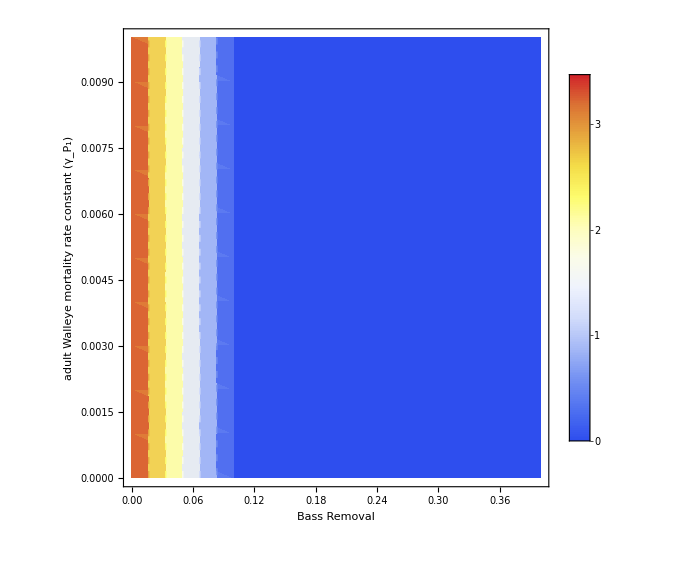

```mathematica
Clear[plot9]
plot9 = ListDensityPlot[biomP1c1, 
Mesh->5,FrameLabel->{{"adult Walleye mortality rate constant (γ_P_1)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,3.47}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1c2]
biomP1c2=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.mj1->mj1in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,mj1in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{mj1in,0.0,0.01,0.001}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1c2[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1c2[[All,3]],_?NumberQ]]
```

5.43754

0

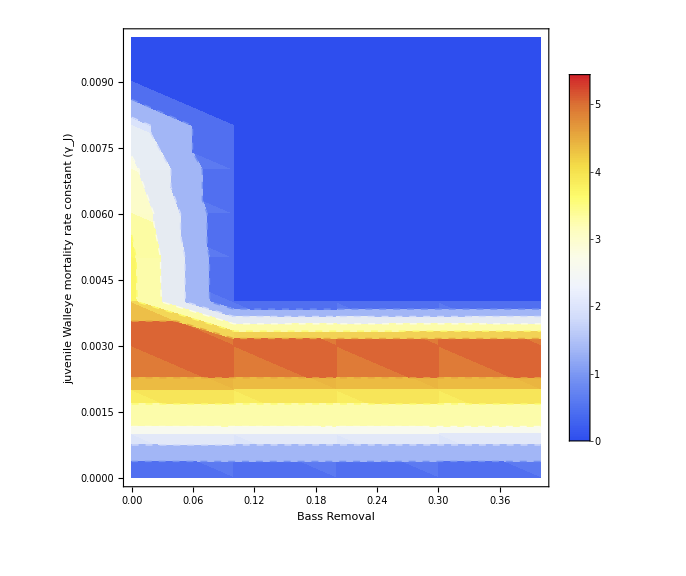

```mathematica
Clear[plot10]
plot10 = ListDensityPlot[biomP1c2, 
Mesh->5,FrameLabel->{{"juvenile Walleye mortality rate constant (γ_J)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,5.44}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1c3]
biomP1c3=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.mp2->mp2in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,mp2in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{mp2in,0.0,0.01,0.001}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1c3[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1c3[[All,3]],_?NumberQ]]
```

6.7022

0

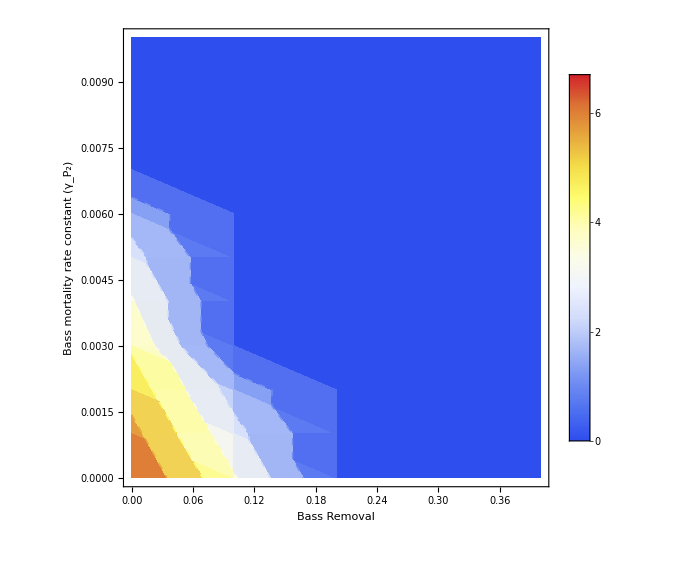

```mathematica
Clear[plot11]
plot11 = ListDensityPlot[biomP1c3, 
Mesh->5,FrameLabel->{{"Bass mortality rate constant (γ_P_2)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,6.70}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1c4]
biomP1c4=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.mc1->mc1in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,mc1in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{mc1in,0.0,0.01,0.001}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1c4[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1c4[[All,3]],_?NumberQ]]
```

3.72212

0

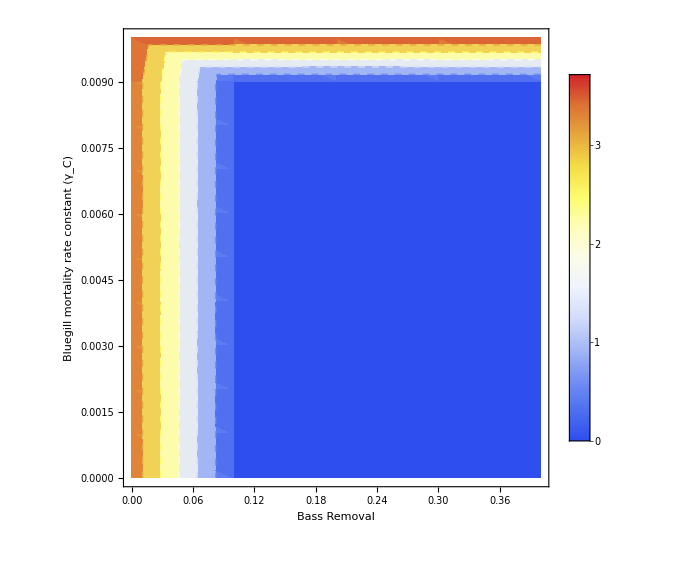

```mathematica
Clear[plot12]
plot12 = ListDensityPlot[biomP1c4, 
Mesh->5,FrameLabel->{{"Bluegill mortality rate constant (γ_C)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,3.72}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

### biomass, P2 harvest, max temp

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1d1]
biomP1d1=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.Tmax1->Tmax1in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,Tmax1in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{Tmax1in,27,38,1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1d1[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1d1[[All,3]],_?NumberQ]]
```

4.01285

0

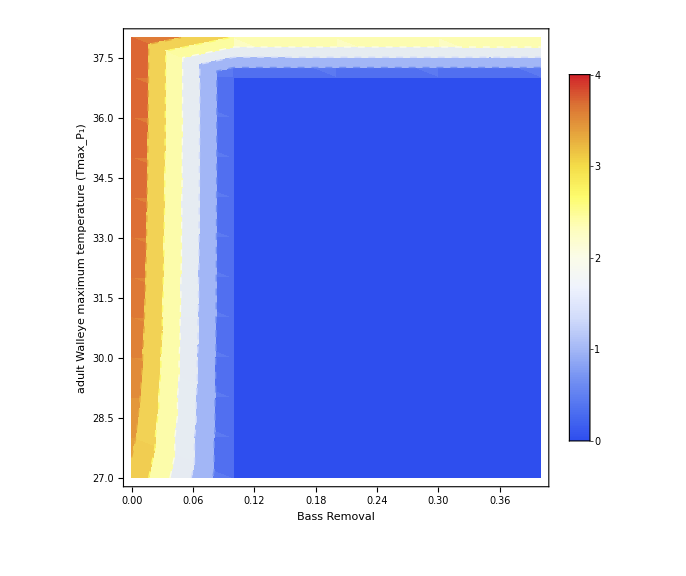

```mathematica
Clear[plot13]
plot13 = ListDensityPlot[biomP1d1, 
Mesh->5,FrameLabel->{{"adult Walleye maximum temperature (Tmax_P_1)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,4.01}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1d2]
biomP1d2=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.Tmax2->Tmax2in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,Tmax2in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{Tmax2in,27,38,1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1d2[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1d2[[All,3]],_?NumberQ]]
```

3.47799

0

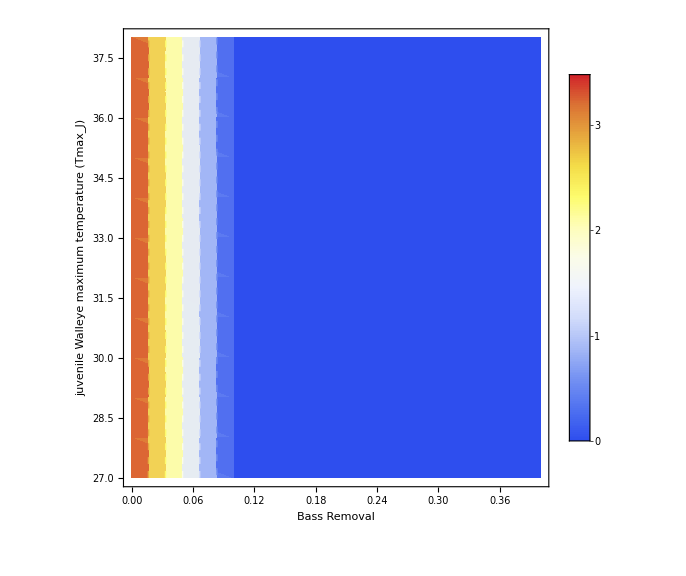

```mathematica
Clear[plot14]
plot14 = ListDensityPlot[biomP1d2, 
Mesh->5,FrameLabel->{{"juvenile Walleye maximum temperature (Tmax_J)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,3.48}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1d3]
biomP1d3=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.Tmax3->Tmax3in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,Tmax3in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{Tmax3in,27,38,1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1d3[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1d3[[All,3]],_?NumberQ]]
```

3.47279

0

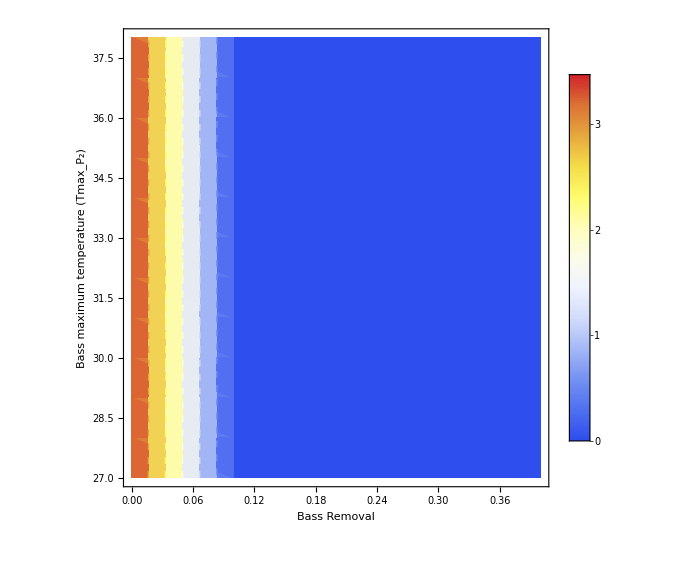

```mathematica
Clear[plot15]
plot15 = ListDensityPlot[biomP1d3, 
Mesh->5,FrameLabel->{{"Bass maximum temperature (Tmax_P_2)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,3.47}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1d4]
biomP1d4=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.Tmax4->Tmax4in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,Tmax4in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{Tmax4in,27,38,1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1d4[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1d4[[All,3]],_?NumberQ]]
```

3.47279

0

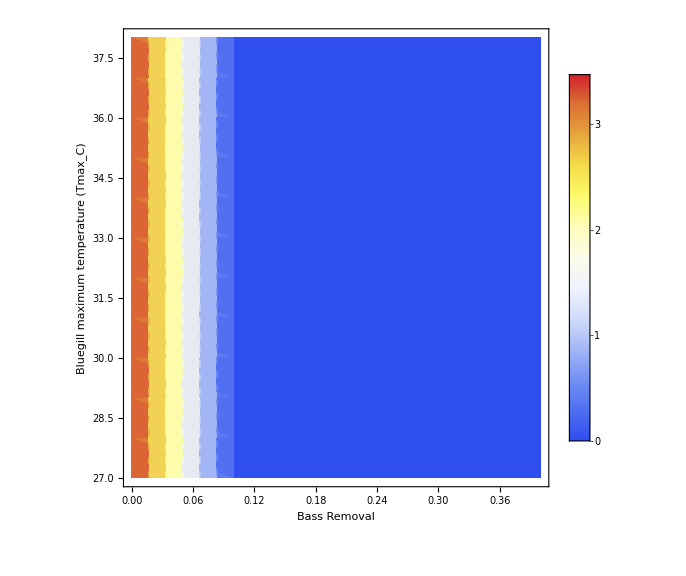

```mathematica
Clear[plot16]
plot16 = ListDensityPlot[biomP1d4, 
Mesh->5,FrameLabel->{{"Bluegill maximum temperature (Tmax_C)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,3.47}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

### biomass, P2 harvest, maturity/somatic growth

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1e1]
biomP1e1=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.som->somin/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,somin,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{somin,0.0,1,0.1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1e1[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1e1[[All,3]],_?NumberQ]]
```

3.47279

0

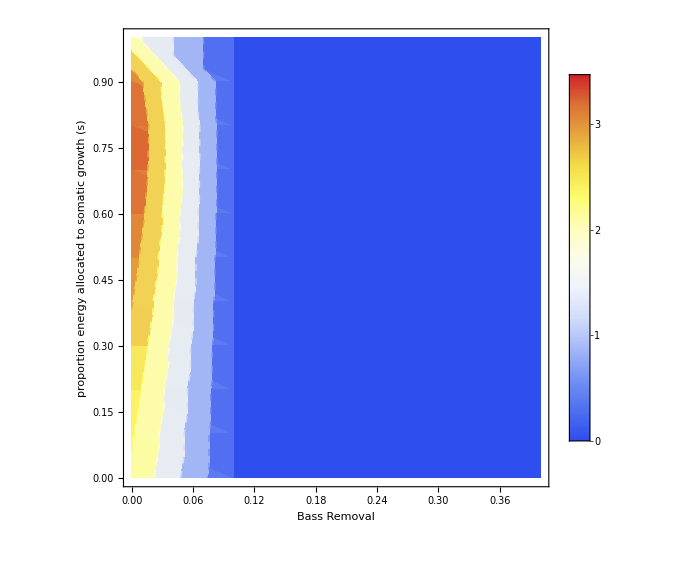

```mathematica
Clear[plot17]
plot17 = ListDensityPlot[biomP1e1, 
Mesh->5,FrameLabel->{{"proportion energy allocated to somatic growth (s)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,3.47}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1e2]
biomP1e2=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T1->25/.mat->matin/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,matin,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{matin,0.0,1,0.1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1e2[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1e2[[All,3]],_?NumberQ]]
```

3.44682

0

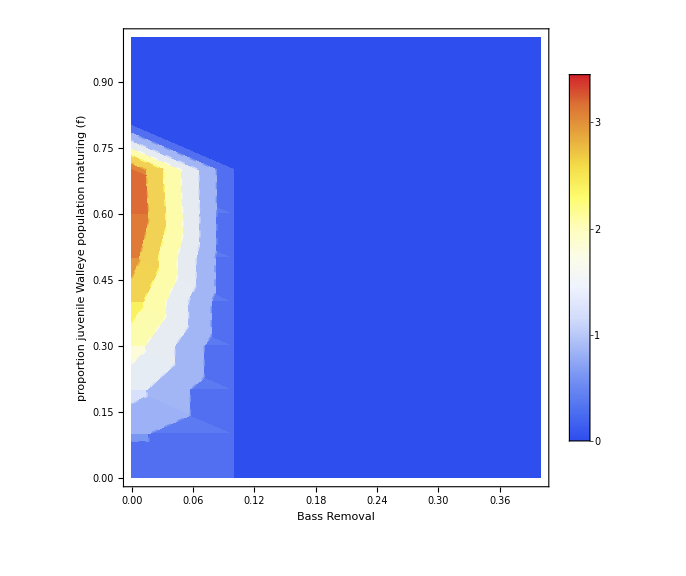

```mathematica
Clear[plot18]
plot18 = ListDensityPlot[biomP1e2, 
Mesh->5,FrameLabel->{{"proportion juvenile Walleye population maturing (f)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,3.45}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

### biomass, P2 harvest, α, β

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1f1]
biomP1f1=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.αw2->αin/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,αin,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{αin,0.0,5,0.1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1f1[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1f1[[All,3]],_?NumberQ]]
```

4.43705

0

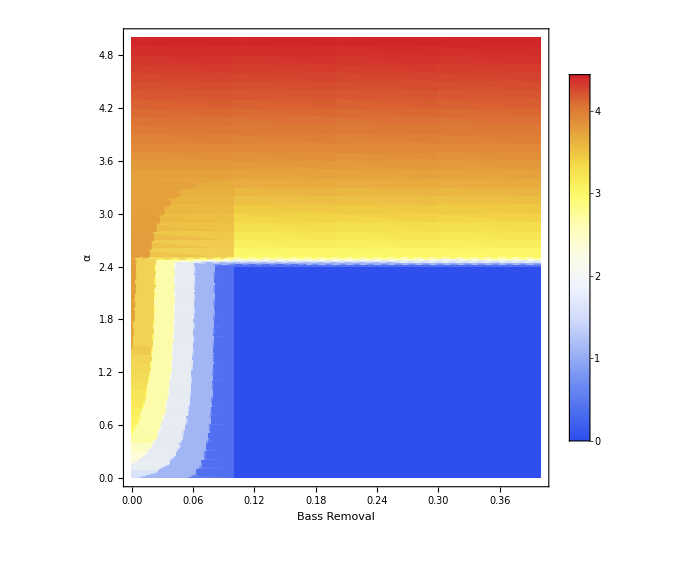

```mathematica
(*not sure if this plot even makes sense (like how I made it)...also, axes are wrong*)
Clear[plot19]
plot19 = ListDensityPlot[biomP1f1, 
Mesh->5,FrameLabel->{{"α"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,4.44}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
Clear[biomP1f2]
biomP1f2=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.βw1->βin/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,βin,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{βin,0.0,0.01,0.001}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1f2[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1f2[[All,3]],_?NumberQ]]
```

3.47295

0

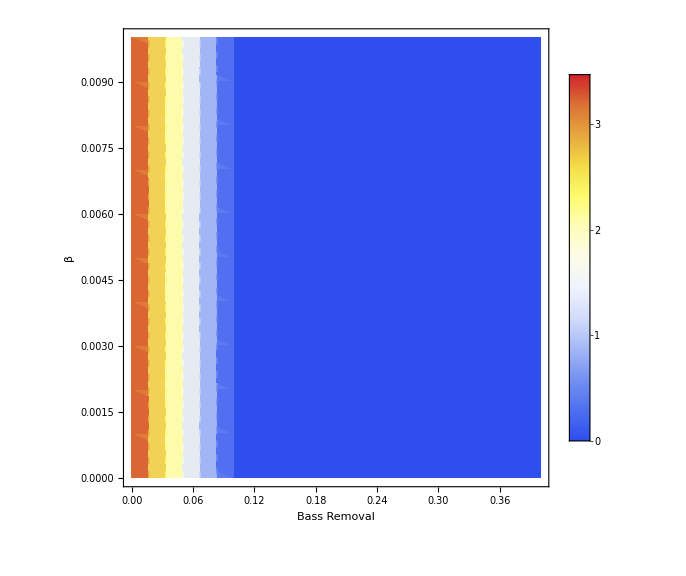

```mathematica
(*not sure if this plot even makes sense (like how I made it)...also, axes are wrong*)
Clear[plot20]
plot20 = ListDensityPlot[biomP1f2, 
Mesh->5,FrameLabel->{{"β"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,3.47}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

### biomass, P2 harvest, σ, σ2

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1g1]
biomP1g1=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.σ->σin/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,σin,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{σin,1,5,1}]],2];
```

```mathematica
Max@Cases[biomP1g1[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1g1[[All,3]],_?NumberQ]]
```

6.7022

0

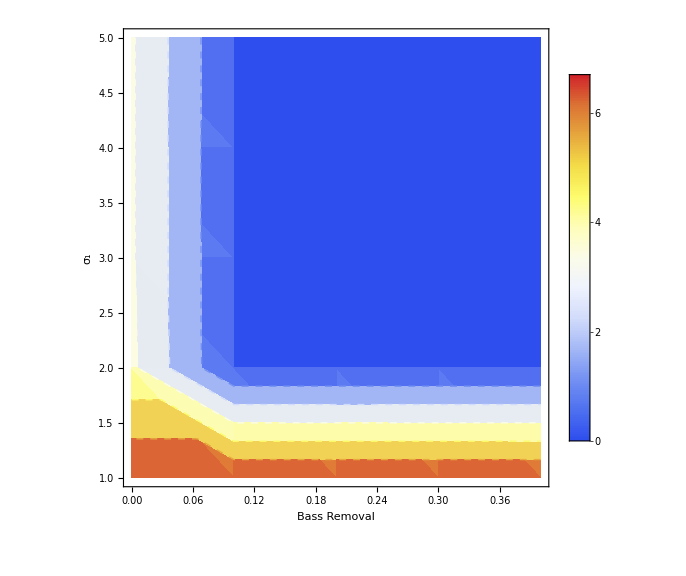

```mathematica
(*not sure if this plot even makes sense (like how I made it)...also, axes are wrong*)
Clear[plot21]
plot21 = ListDensityPlot[biomP1g1, 
Mesh->5,FrameLabel->{{"σ_1"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,6.70}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
Clear[biomP1fg2]
biomP1g2=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.σ2->σ2in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,σ2in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{σ2in,1,5,1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1g2[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1g2[[All,3]],_?NumberQ]]
```

3.47279

0

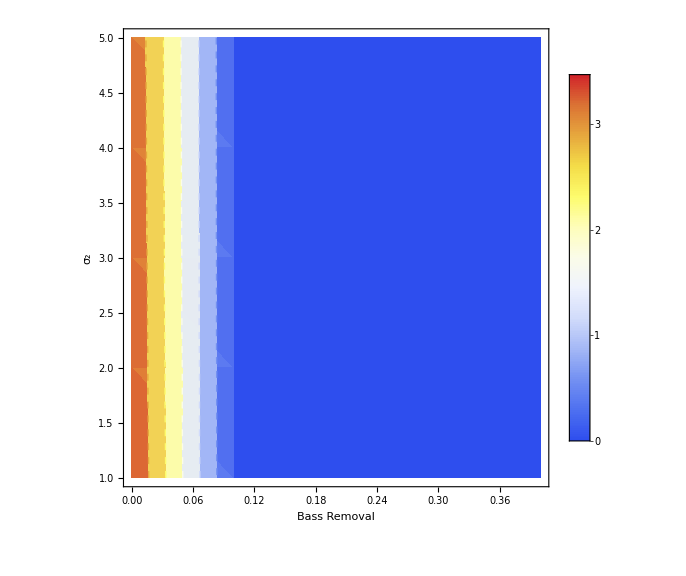

```mathematica
(*not sure if this plot even makes sense (like how I made it)...also, axes are wrong*)
Clear[plot22]
plot22 = ListDensityPlot[biomP1g2, 
Mesh->5,FrameLabel->{{"σ_2"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,3.47}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

### biomass, P2 harvest, P1, J1, C1 harvest

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1h1]
biomP1h1=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.h1->h1in/.h3->h3in/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{h3in,h1in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{h3in,0,0.4,0.1},{h1in,0,0.4,0.1}]],2];
```

```mathematica
Max@Cases[biomP1h1[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1h1[[All,3]],_?NumberQ]]
```

9.26113

0

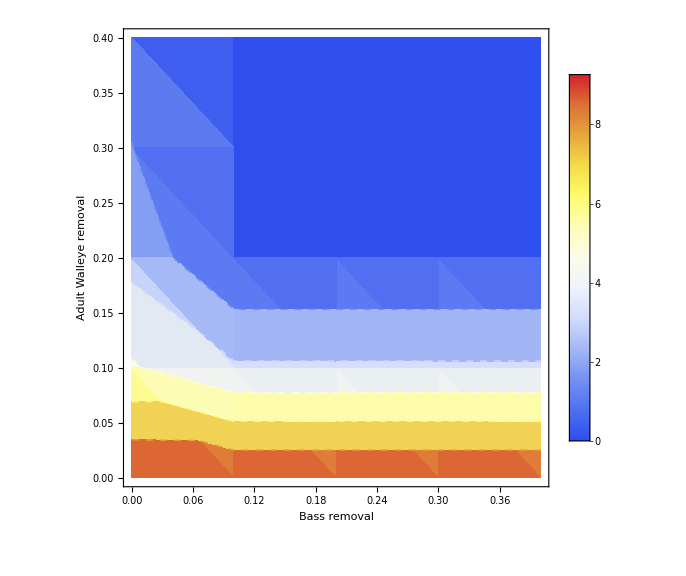

```mathematica
(*not sure if this plot even makes sense (like how I made it)...also, axes are wrong*)
Clear[plot23]
plot23 = ListDensityPlot[biomP1h1, 
Mesh->5,FrameLabel->{{"Adult Walleye removal"},{"Bass removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,9.26}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
Clear[biomP1h2]
biomP1h2=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.h4->h4in/.h3->h3in/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{h3in,h4in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{h3in,0,0.4,0.1},{h4in,0,0.4,0.1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1h2[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1h2[[All,3]],_?NumberQ]]
```

6.7022

0

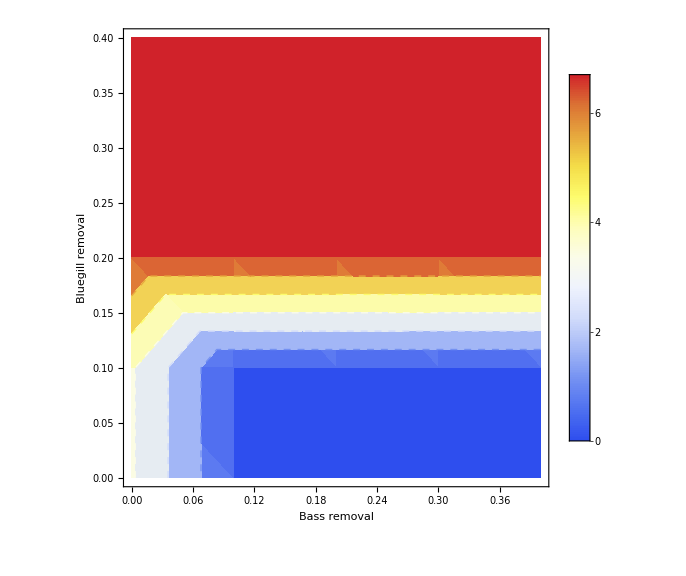

```mathematica
(*not sure if this plot even makes sense (like how I made it)...also, axes are wrong*)
Clear[plot24]
plot24 = ListDensityPlot[biomP1h2, 
Mesh->5,FrameLabel->{{"Bluegill removal"},{"Bass removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,6.70}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
Clear[biomP1h3]
biomP1h3=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.h2->h2in/.h3->h3in/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{h3in,h2in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{h3in,0,0.4,0.1},{h2in,0,0.4,0.1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1h3[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1h3[[All,3]],_?NumberQ]]
```

3.47279

0

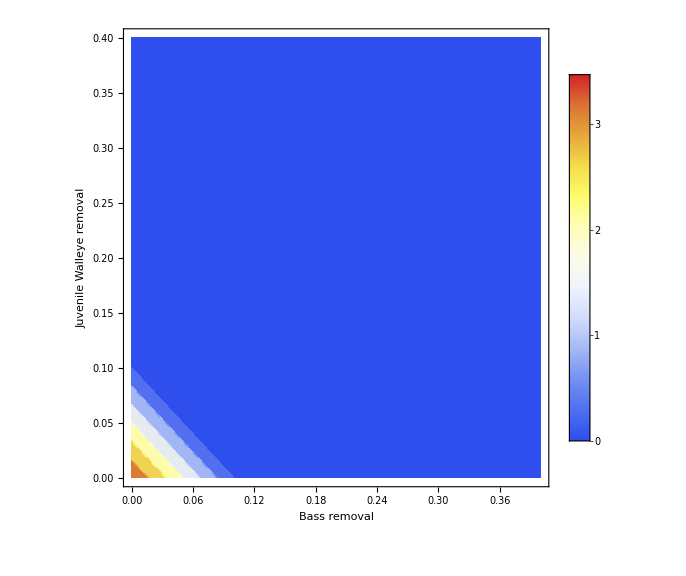

```mathematica
(*not sure if this plot even makes sense (like how I made it)...also, axes are wrong*)
Clear[plot25]
plot25 = ListDensityPlot[biomP1h3, 
Mesh->5,FrameLabel->{{"Juvenile Walleye removal"},{"Bass removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,3.47}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

### biomass, P2 harvest, opt temp

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1i1]
biomP1i1=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.Topt1->Topt1in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,Topt1in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{Topt1in,15,35,1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1i1[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1i1[[All,3]],_?NumberQ]]
```

4.09974

0

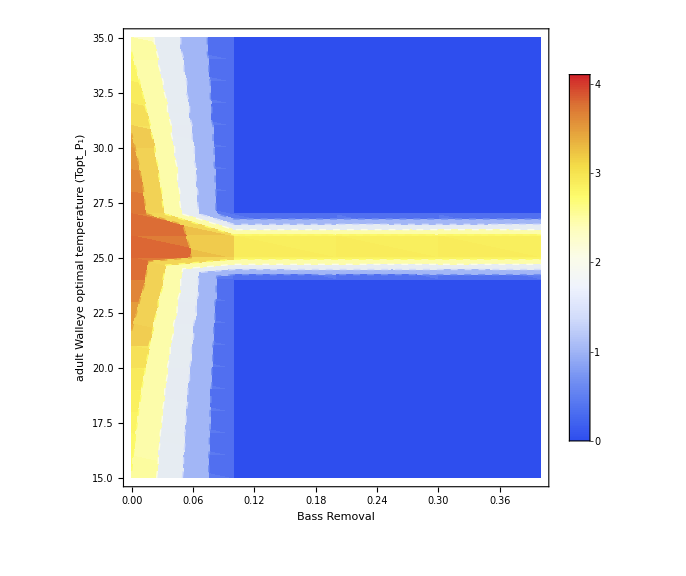

```mathematica
Clear[plot26]
plot26 = ListDensityPlot[biomP1i1, 
Mesh->5,FrameLabel->{{"adult Walleye optimal temperature (Topt_P_1)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,4.10}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1i2]
biomP1i2=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.Topt2->Topt2in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,Topt2in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{Topt2in,15,35,1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1i2[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1i2[[All,3]],_?NumberQ]]
```

3.47279

0

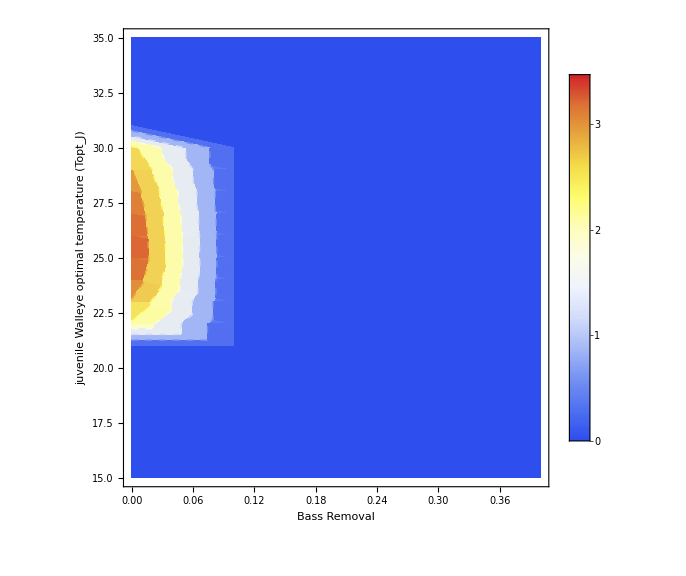

```mathematica
Clear[plot27]
plot27 = ListDensityPlot[biomP1i2, 
Mesh->5,FrameLabel->{{"juvenile Walleye optimal temperature (Topt_J)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,3.47}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1i3]
biomP1i3=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.Topt3->Topt3in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,Topt3in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{Topt3in,15,35,1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1i3[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1i3[[All,3]],_?NumberQ]]
```

3.67849

0

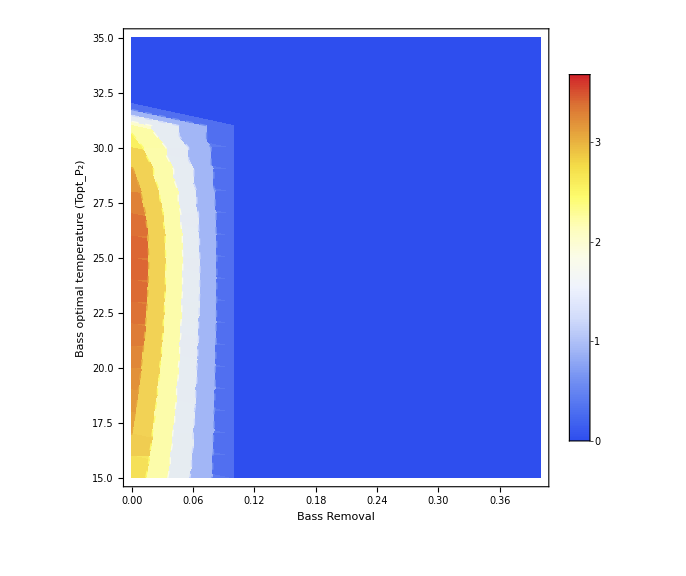

```mathematica
Clear[plot28]
plot28 = ListDensityPlot[biomP1i3, 
Mesh->5,FrameLabel->{{"Bass optimal temperature (Topt_P_2)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,3.68}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[biomP1i4]
biomP1i4=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T->25/.Topt4->Topt4in/.h3->hin/.params/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{hin,Topt4in,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{hin,0,0.4,0.1},{Topt4in,15,35,1}]],2];
(*h=0 here, will do 0.4 in next one and then divid separately*)
```

```mathematica
Max@Cases[biomP1i4[[All,3]],Except[Infinity|Indeterminate]]
Min[Cases[biomP1i4[[All,3]],_?NumberQ]]
```

6.7022

0

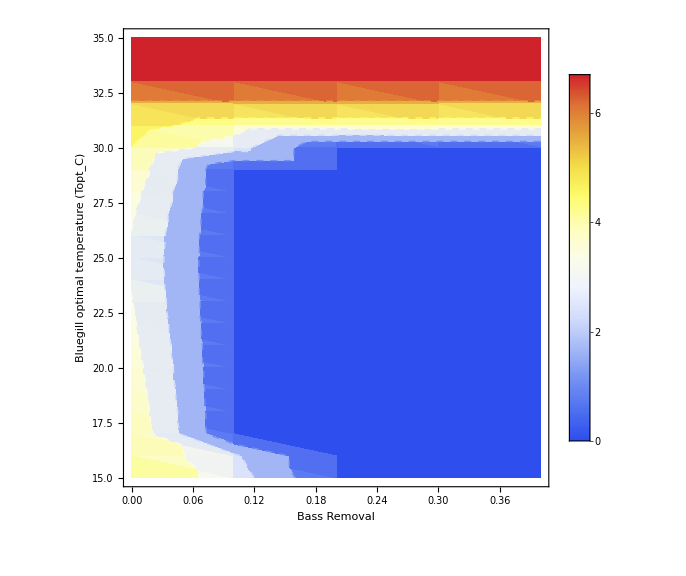

```mathematica
Clear[plot29]
plot29 = ListDensityPlot[biomP1i4, 
Mesh->5,FrameLabel->{{"Bluegill optimal temperature (Topt_C)"},{"Bass Removal"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{0,6.70}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial",FontColor->"Black"]]
```

## Additional Results

## Alt consumer (C_1) parameters

### Parameters - Yellow Perch

```mathematica
(*for TPC functions*)
Clear[paramsYP]
paramsYP = Dispatch[{
σ -> 5, (*increasing makes slope shallower*)
σ2 -> 1, (*increasing makes slope shallower*)

ap1c1 -> 0.02, (*P1 attack on C1, FB4 0.0387,0.04*)
ap1r2 -> 0.005, (*P1 attack on R2*)
aj1 -> 0.08, (*J1 attack on resource, FB4 0.13*)
ac1 -> 0.08, (*C1 attack on resource, FB4 0.052*)
ap2c1 -> 0.02, (*P2 attac on C1, FB4 0.035*,0.04*)
ap2j1 -> 0.001, (*P2 attack on J1*)

mp1 -> 0.004, (*0.001*)
mj1 -> 0.005, 
mp2 -> 0.004, 
mc1 -> 0.005, 

Topt1 -> 22, (* P1 optimal temp (adult Walleye) - from FB4*)
Topt2 -> 25, (* J1 optimal temp (juv Walleye) - from FB4*)
Topt3 -> 27.5, (* P2 optimal temp (largemouth bass)- from FB4; Smallmouth would be 29 *)
Topt4 -> 25, (* C1 optimal temp (Yellow Perch) - from Hasnain*)

Tmax1 -> 28, (* P1 optimal temp (adult Walleye) - from FB4*)
Tmax2 -> 28, (* J1 optimal temp (juv Walleye) - from FB4*)
Tmax3 -> 37, (* P2 optimal temp (Largemouth Bass)- from FB4; Smallmouth would be 36 *)
Tmax4 -> 35, (* C1 optimal temp (Yellow Perch) - from Hasnain*)

T->25
}];
```

### Parameters - Golden Shiner

```mathematica
(*for TPC functions*)
Clear[paramsGS]
paramsGS = Dispatch[{
σ -> 5, (*increasing makes slope shallower*)
σ2 -> 1, (*increasing makes slope shallower*)

ap1c1 -> 0.02, (*P1 attack on C1, FB4 0.0387,0.04*)
ap1r2 -> 0.005, (*P1 attack on R2*)
aj1 -> 0.08, (*J1 attack on resource, FB4 0.13*)
ac1 -> 0.08, (*C1 attack on resource, FB4 0.052*)
ap2c1 -> 0.02, (*P2 attac on C1, FB4 0.035*,0.04*)
ap2j1 -> 0.001, (*P2 attack on J1*)

mp1 -> 0.004, (*0.001*)
mj1 -> 0.005, 
mp2 -> 0.004, 
mc1 -> 0.005, 

Topt1 -> 22, (* P1 optimal temp (adult Walleye) - from FB4*)
Topt2 -> 25, (* J1 optimal temp (juv Walleye) - from FB4*)
Topt3 -> 27.5, (* P2 optimal temp (largemouth bass)- from FB4; Smallmouth would be 29 *)
Topt4 -> 25, (* C1 optimal temp (Golden Shiner) - from Hasnain*)

Tmax1 -> 28, (* P1 optimal temp (adult Walleye) - from FB4*)
Tmax2 -> 28, (* J1 optimal temp (juv Walleye) - from FB4*)
Tmax3 -> 37, (* P2 optimal temp (Largemouth Bass)- from FB4; Smallmouth would be 36 *)
Tmax4 -> 32, (* C1 optimal temp (Golden Shiner) - from Hasnain*)

T->25
}];
```

### Parameters - Black Crappie

```mathematica
(*for TPC functions*)
Clear[paramsBC]
paramsBC = Dispatch[{
σ -> 5, (*increasing makes slope shallower*)
σ2 -> 1, (*increasing makes slope shallower*)

ap1c1 -> 0.02, (*P1 attack on C1, FB4 0.0387,0.04*)
ap1r2 -> 0.005, (*P1 attack on R2*)
aj1 -> 0.08, (*J1 attack on resource, FB4 0.13*)
ac1 -> 0.08, (*C1 attack on resource, FB4 0.052*)
ap2c1 -> 0.02, (*P2 attac on C1, FB4 0.035*,0.04*)
ap2j1 -> 0.001, (*P2 attack on J1*)

mp1 -> 0.004, (*0.001*)
mj1 -> 0.005, 
mp2 -> 0.004, 
mc1 -> 0.005, 

Topt1 -> 22, (* P1 optimal temp (adult Walleye) - from FB4*)
Topt2 -> 25, (* J1 optimal temp (juv Walleye) - from FB4*)
Topt3 -> 27.5, (* P2 optimal temp (largemouth bass)- from FB4; Smallmouth would be 29 *)
Topt4 -> 18, (* C1 optimal temp (Black Crappie) - from Hasnain*)

Tmax1 -> 28, (* P1 optimal temp (adult Walleye) - from FB4*)
Tmax2 -> 28, (* J1 optimal temp (juv Walleye) - from FB4*)
Tmax3 -> 37, (* P2 optimal temp (Largemouth Bass)- from FB4; Smallmouth would be 36 *)
Tmax4 -> 34.9, (* C1 optimal temp (Black Crappie) - from Hasnain*)

T->25
}];
```

### Parameters - Pumpkinseed

```mathematica
(*for TPC functions*)
Clear[paramsPS]
paramsPS = Dispatch[{
σ -> 5, (*increasing makes slope shallower*)
σ2 -> 1, (*increasing makes slope shallower*)

ap1c1 -> 0.02, (*P1 attack on C1, FB4 0.0387,0.04*)
ap1r2 -> 0.005, (*P1 attack on R2*)
aj1 -> 0.08, (*J1 attack on resource, FB4 0.13*)
ac1 -> 0.08, (*C1 attack on resource, FB4 0.052*)
ap2c1 -> 0.02, (*P2 attac on C1, FB4 0.035*,0.04*)
ap2j1 -> 0.001, (*P2 attack on J1*)

mp1 -> 0.004, (*0.001*)
mj1 -> 0.005, 
mp2 -> 0.004, 
mc1 -> 0.005, 

Topt1 -> 22, (* P1 optimal temp (adult Walleye) - from FB4*)
Topt2 -> 25, (* J1 optimal temp (juv Walleye) - from FB4*)
Topt3 -> 27.5, (* P2 optimal temp (largemouth bass)- from FB4; Smallmouth would be 29 *)
Topt4 -> 25, (* C1 optimal temp (Pumpkinseed) - from Hasnain*)

Tmax1 -> 28, (* P1 optimal temp (adult Walleye) - from FB4*)
Tmax2 -> 28, (* J1 optimal temp (juv Walleye) - from FB4*)
Tmax3 -> 37, (* P2 optimal temp (Largemouth Bass)- from FB4; Smallmouth would be 36 *)
Tmax4 -> 37.6, (* C1 optimal temp (Pumpkinseed) - from Hasnain*)

T->25
}];
```

## Alt consumer (C_1) TPC plots

Just Consumers

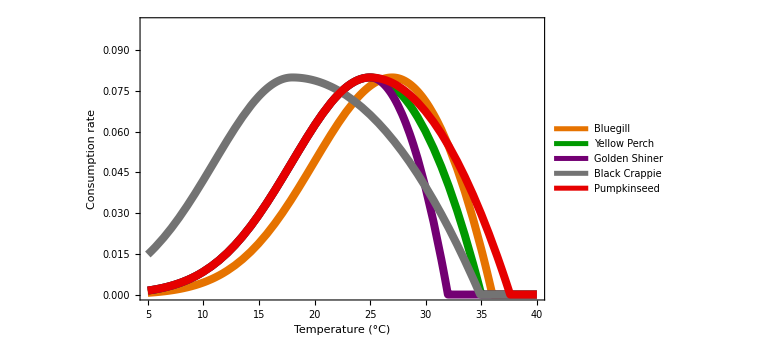

```mathematica
Plot[{aC1[Tx]/.params, aC1[Tx]/.paramsYP, aC1[Tx]/.paramsGS, aC1[Tx]/.paramsBC, aC1[Tx]/.paramsPS}, {Tx,5,40}, PlotRange->{{5,40},{0,0.10}}, PlotLegends->{"Bluegill", "Yellow Perch", "Golden Shiner", "Black Crappie", "Pumpkinseed"}, Frame->True, 
FrameLabel->{{"Consumption rate",""},{"Temperature (°C)",""}}, PlotStyle -> {{Thickness[0.01], Darker[Orange,0.1]}, {Thickness[0.01], Darker[Green,0.4]},{Thickness[0.01],Darker[Purple,0.1]}, {Thickness[0.01], Darker[Gray,0.1]}, {Thickness[0.01], Darker[Red,0.1]}}, 
ImageSize->Large, LabelStyle->Directive[FontSize->20, FontFamily->"Arial", FontColor->"Black"]]
```

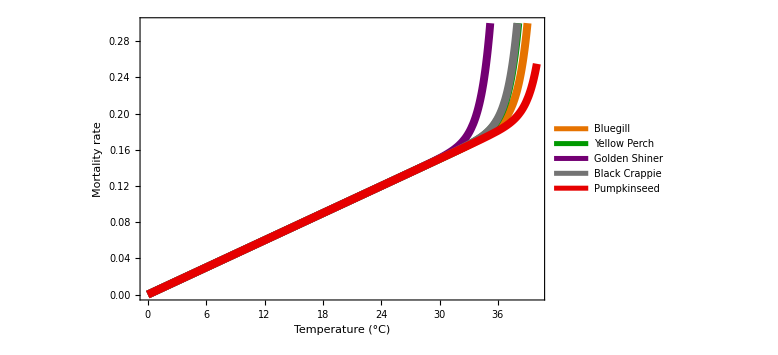

```mathematica
Plot[{mC1[Tx]/.params, mC1[Tx]/.paramsYP, mC1[Tx]/.paramsGS, mC1[Tx]/.paramsBC, mC1[Tx]/.paramsPS},{Tx,0,40}, PlotLegends->{"Bluegill", "Yellow Perch", "Golden Shiner", "Black Crappie", "Pumpkinseed"}, PlotRange->{{0,40},{0,0.3}}, Frame->True, 
FrameLabel->{{"Mortality rate",""},{"Temperature (°C)",""}}, PlotStyle ->{{Thickness[0.01], Darker[Orange,0.1]}, {Thickness[0.01], Darker[Green,0.4]},{Thickness[0.01],Darker[Purple,0.1]}, {Thickness[0.01], Darker[Gray,0.1]}, {Thickness[0.01], Darker[Red,0.1]}}, 
ImageSize->Large, LabelStyle->Directive[FontSize->20, FontFamily->"Arial", FontColor->"Black"]]
```

## Alt consumer (C_1) P_1 Extinction Temperature

### Yellow Perch as consumer

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[ExtMeanP1b]
ExtMeanP1b=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.ap2j1->ap2j1in/.T->val/.h3->hin/.paramsYP/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{ap2j1in,hin,val,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{ap2j1in,0.0,0.04,0.01},{val,21,35,1},{hin,0,0.5,0.1}]],3];
(*Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
```

```mathematica
ExtMeanP1b;
```

Below is exporting the data for the heat map so that I don’t have to run the long code every time. If ANYTHING changes above, the code will have to be re-run...note that this data is called ext3. the other versions we’ve been using are ext2 and ext1

```mathematica
Export["ext3b.csv",ExtMeanP1b,"Table"];
```

```mathematica
Clear[data1b]
data1b=Import["ext3b.csv", "Table"];
```

```mathematica
(*This is for the line plot...Here the code removes cases that correspond to each a22 value (was Tmax value 28-35)*)
P1se1b =Drop[Cases[data1b,{0.00,_,_,_}],None,1];
P1se2b =Drop[Cases[data1b,{0.01,_,_,_}],None,1];
P1se3b =Drop[Cases[data1b,{0.02,_,_,_}],None,1];
P1se4b =Drop[Cases[data1b,{0.03,_,_,_}],None,1];
P1se5b =Drop[Cases[data1b,{0.04,_,_,_}],None,1];
```

```mathematica
(*Here the code should be extracting the data for the first case where density equals 0*)
P1ext1b= Take[Table[FirstCase[P1se1b,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext2b= Take[Table[FirstCase[P1se2b,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext3b= Take[Table[FirstCase[P1se3b,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext4b= Take[Table[FirstCase[P1se4b,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext5b= Take[Table[FirstCase[P1se5b,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
```

the numbers refer to the bass attack rate on juvenile walleye (0.0-0.4)

```mathematica
(*This is where you start the heat map plot*)
P1x1b =Cases[data1b,{0.00,_,_,_}];
P1x2b =Cases[data1b,{0.01,_,_,_}];
P1x3b =Cases[data1b,{0.02,_,_,_}];
P1x4b =Cases[data1b,{0.03,_,_,_}];
P1x5b =Cases[data1b,{0.04,_,_,_}];
```

Below is where you get the extinction temps for each attack rate (bass on juvenile); 0.0-0.4. The second set of brackets is for the bass removal rates (0 to 5 in increments of 0.1 - I (LJ) changed it from 0.01 to 0.1 to make it faster. The code is pulling the temperature at which the outcome goes to zero; showing all three columns of all combinations of attack rate and harvest.

```mathematica
P1T1b= Take[Table[FirstCase[P1x1b,{0.00,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T2b= Take[Table[FirstCase[P1x2b,{0.01,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T3b= Take[Table[FirstCase[P1x3b,{0.02,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T4b= Take[Table[FirstCase[P1x4b,{0.03,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T5b= Take[Table[FirstCase[P1x5b,{0.04,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
```

```mathematica
(*Here I join into one list on data*)
extdata1b = Join[P1T1b,P1T2b,P1T3b,P1T4b,P1T5b];
Max[extdata1b[[All,3]]]
Min[extdata1b[[All,3]]]
```

27

21

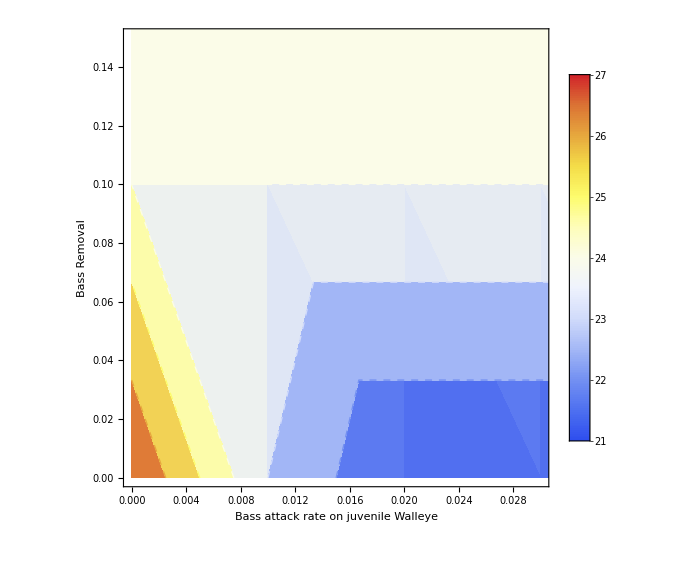

```mathematica
Clear[plot1b] (*same plot as above, just different axes*)
plot1b = ListDensityPlot[extdata1b, 
Mesh->5,FrameLabel->{{"Bass Removal"},{"Bass attack rate on juvenile Walleye"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->{{0,0.03},{0,0.15}},
PlotLegends-> BarLegend[{"TemperatureMap",{21,27}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial", FontColor->Black]]
```

### Golden Shiner as consumer

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[ExtMeanP1c]
ExtMeanP1c=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.ap2j1->ap2j1in/.T->val/.h3->hin/.paramsGS/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{ap2j1in,hin,val,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{ap2j1in,0.0,0.04,0.01},{val,21,35,1},{hin,0,0.5,0.1}]],3];
(*Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
```

```mathematica
ExtMeanP1c;
```

Below is exporting the data for the heat map so that I don’t have to run the long code every time. If ANYTHING changes above, the code will have to be re-run...note that this data is called ext3. the other versions we’ve been using are ext2 and ext1

```mathematica
Export["ext3c.csv",ExtMeanP1c,"Table"];
```

```mathematica
Clear[data1c]
data1c=Import["ext3c.csv", "Table"];
```

```mathematica
(*This is for the line plot...Here the code removes cases that correspond to each a22 value (was Tmax value 28-35)*)
P1se1c =Drop[Cases[data1c,{0.00,_,_,_}],None,1];
P1se2c =Drop[Cases[data1c,{0.01,_,_,_}],None,1];
P1se3c =Drop[Cases[data1c,{0.02,_,_,_}],None,1];
P1se4c =Drop[Cases[data1c,{0.03,_,_,_}],None,1];
P1se5c =Drop[Cases[data1c,{0.04,_,_,_}],None,1];
```

```mathematica
(*Here the code should be extracting the data for the first case where density equals 0*)
P1ext1c= Take[Table[FirstCase[P1se1c,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext2c= Take[Table[FirstCase[P1se2c,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext3c= Take[Table[FirstCase[P1se3c,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext4c= Take[Table[FirstCase[P1se4c,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext5c= Take[Table[FirstCase[P1se5c,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
```

the numbers refer to the bass attack rate on juvenile walleye (0.0-0.4)

```mathematica
(*This is where you start the heat map plot*)
P1x1c =Cases[data1c,{0.00,_,_,_}];
P1x2c =Cases[data1c,{0.01,_,_,_}];
P1x3c =Cases[data1c,{0.02,_,_,_}];
P1x4c =Cases[data1c,{0.03,_,_,_}];
P1x5c =Cases[data1c,{0.04,_,_,_}];
```

Below is where you get the extinction temps for each attack rate (bass on juvenile); 0.0-0.4. The second set of brackets is for the bass removal rates (0 to 5 in increments of 0.1 - I (LJ) changed it from 0.01 to 0.1 to make it faster. The code is pulling the temperature at which the outcome goes to zero; showing all three columns of all combinations of attack rate and harvest.

```mathematica
P1T1c= Take[Table[FirstCase[P1x1c,{0.00,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T2c= Take[Table[FirstCase[P1x2c,{0.01,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T3c= Take[Table[FirstCase[P1x3c,{0.02,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T4c= Take[Table[FirstCase[P1x4c,{0.03,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T5c= Take[Table[FirstCase[P1x5c,{0.04,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
```

```mathematica
(*Here I join into one list on data*)
extdata1c = Join[P1T1c,P1T2c,P1T3c,P1T4c,P1T5c];
Max[extdata1c[[All,3]]]
Min[extdata1c[[All,3]]]
```

27

21

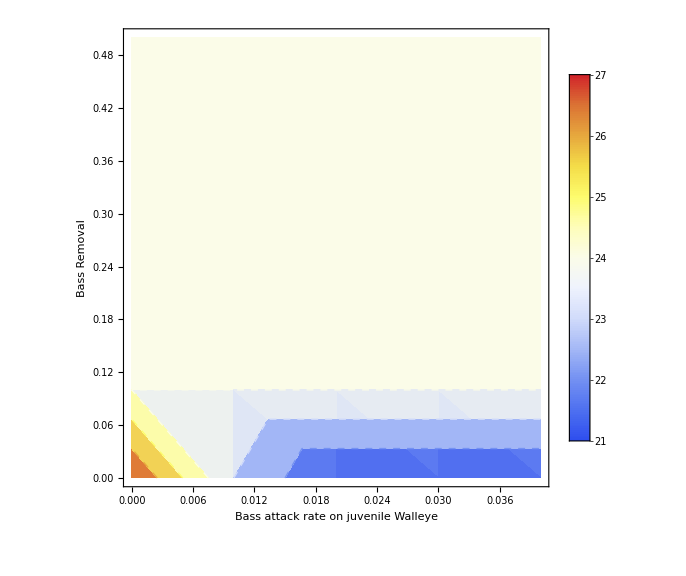

```mathematica
Clear[plotc]
plotc = ListDensityPlot[extdata1c, 
Mesh->5,FrameLabel->{{"Bass Removal"},{"Bass attack rate on juvenile Walleye"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{21,27}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial", FontColor->Black]]
```

```mathematica
Clear[plot2c] (*same plot as above, just different axes*)
plot2c = ListDensityPlot[extdata1c, 
Mesh->5,FrameLabel->{{"Bass Removal"},{"Bass attack rate on juvenile Walleye"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->{{0,0.03},{0,0.15}},
PlotLegends-> BarLegend[{"TemperatureMap",{21,27}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial", FontColor->Black]]
```

-Graphics-

### Black Crappie as consumer

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[ExtMeanP1d]
ExtMeanP1d=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.ap2j1->ap2j1in/.T->val/.h3->hin/.paramsBC/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{ap2j1in,hin,val,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{ap2j1in,0.0,0.04,0.01},{val,21,35,1},{hin,0,0.5,0.1}]],3];
(*Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
```

```mathematica
ExtMeanP1d;
```

Below is exporting the data for the heat map so that I don’t have to run the long code every time. If ANYTHING changes above, the code will have to be re-run...note that this data is called ext3. the other versions we’ve been using are ext2 and ext1

```mathematica
Export["ext3d.csv",ExtMeanP1d,"Table"];
```

```mathematica
Clear[data1d]
data1d=Import["ext3d.csv", "Table"];
```

```mathematica
(*This is for the line plot...Here the code removes cases that correspond to each a22 value (was Tmax value 28-35)*)
P1se1d =Drop[Cases[data1d,{0.00,_,_,_}],None,1];
P1se2d =Drop[Cases[data1d,{0.01,_,_,_}],None,1];
P1se3d =Drop[Cases[data1d,{0.02,_,_,_}],None,1];
P1se4d =Drop[Cases[data1d,{0.03,_,_,_}],None,1];
P1se5d =Drop[Cases[data1d,{0.04,_,_,_}],None,1];
```

```mathematica
(*Here the code should be extracting the data for the first case where density equals 0*)
P1ext1d= Take[Table[FirstCase[P1se1d,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext2d= Take[Table[FirstCase[P1se2d,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext3d= Take[Table[FirstCase[P1se3d,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext4d= Take[Table[FirstCase[P1se4d,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext5d= Take[Table[FirstCase[P1se5d,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
```

the numbers refer to the bass attack rate on juvenile walleye (0.0-0.4)

```mathematica
(*This is where you start the heat map plot*)
P1x1d =Cases[data1d,{0.00,_,_,_}];
P1x2d =Cases[data1d,{0.01,_,_,_}];
P1x3d =Cases[data1d,{0.02,_,_,_}];
P1x4d =Cases[data1d,{0.03,_,_,_}];
P1x5d =Cases[data1d,{0.04,_,_,_}];
```

Below is where you get the extinction temps for each attack rate (bass on juvenile); 0.0-0.4. The second set of brackets is for the bass removal rates (0 to 5 in increments of 0.1 - I (LJ) changed it from 0.01 to 0.1 to make it faster. The code is pulling the temperature at which the outcome goes to zero; showing all three columns of all combinations of attack rate and harvest.

```mathematica
P1T1d= Take[Table[FirstCase[P1x1d,{0.00,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T2d= Take[Table[FirstCase[P1x2d,{0.01,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T3d= Take[Table[FirstCase[P1x3d,{0.02,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T4d= Take[Table[FirstCase[P1x4d,{0.03,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T5d= Take[Table[FirstCase[P1x5d,{0.04,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
```

```mathematica
(*Here I join into one list on data*)
extdata1d = Join[P1T1d,P1T2d,P1T3d,P1T4d,P1T5d];
Max[extdata1d[[All,3]]]
Min[extdata1d[[All,3]]]
```

27

21

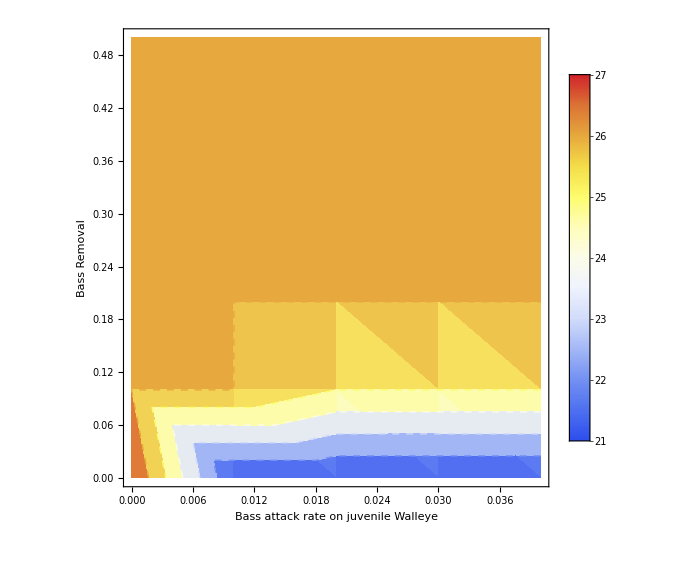

```mathematica
Clear[plot1d]
plot1d = ListDensityPlot[extdata1d, 
Mesh->5,FrameLabel->{{"Bass Removal"},{"Bass attack rate on juvenile Walleye"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->All,
PlotLegends-> BarLegend[{"TemperatureMap",{21,27}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial", FontColor->Black]]
```

### Pumpkinseed as consumer

```mathematica
(*This is the code for the heat map. Note there are three variables--LJ trying different AccuracyGoal (was 30) and PrecisionGoal (was 10), 
the range of val (was 5-40) and hin step size (was 0.01)*)
Clear[ExtMeanP1e]
ExtMeanP1e=Flatten[Module[{sol1},
Table[sol1=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.ap2j1->ap2j1in/.T->val/.h3->hin/.paramsPS/.rates,{R1,C1,J1,P1,P2,R2},{t,0,5000},AccuracyGoal->10, PrecisionGoal->5, MaxStepSize->0.1,MaxSteps->100000];
Thread[{ap2j1in,hin,val,Chop[Mean[P1[Range[4000,5000]]]/.sol1,10^-2]}],{ap2j1in,0.0,0.04,0.01},{val,21,35,1},{hin,0,0.5,0.1}]],3];
(*Note that these will need to be adjusted based on the hin length. Here it is 2 but for more levels of hin will need to Take[] after more spaces*)
```

```mathematica
ExtMeanP1e;
```

Below is exporting the data for the heat map so that I don’t have to run the long code every time. If ANYTHING changes above, the code will have to be re-run...note that this data is called ext3. the other versions we’ve been using are ext2 and ext1

```mathematica
Export["ext3e.csv",ExtMeanP1e,"Table"];
```

```mathematica
Clear[data1e]
data1e=Import["ext3e.csv", "Table"];
```

```mathematica
(*This is for the line plot...Here the code removes cases that correspond to each a22 value (was Tmax value 28-35)*)
P1se1e =Drop[Cases[data1e,{0.00,_,_,_}],None,1];
P1se2e =Drop[Cases[data1e,{0.01,_,_,_}],None,1];
P1se3e =Drop[Cases[data1e,{0.02,_,_,_}],None,1];
P1se4e =Drop[Cases[data1e,{0.03,_,_,_}],None,1];
P1se5e =Drop[Cases[data1e,{0.04,_,_,_}],None,1];
```

```mathematica
(*Here the code should be extracting the data for the first case where density equals 0*)
P1ext1e= Take[Table[FirstCase[P1se1e,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext2e= Take[Table[FirstCase[P1se2e,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext3e= Take[Table[FirstCase[P1se3e,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext4e= Take[Table[FirstCase[P1se4e,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
P1ext5e= Take[Table[FirstCase[P1se5e,{x,_,0}],{x,0,0.5,0.1}][[All,1;;2]]];
```

the numbers refer to the bass attack rate on juvenile walleye (0.0-0.4)

```mathematica
(*This is where you start the heat map plot*)
P1x1e =Cases[data1e,{0.00,_,_,_}];
P1x2e =Cases[data1e,{0.01,_,_,_}];
P1x3e =Cases[data1e,{0.02,_,_,_}];
P1x4e =Cases[data1e,{0.03,_,_,_}];
P1x5e =Cases[data1e,{0.04,_,_,_}];
```

Below is where you get the extinction temps for each attack rate (bass on juvenile); 0.0-0.4. The second set of brackets is for the bass removal rates (0 to 5 in increments of 0.1 - I (LJ) changed it from 0.01 to 0.1 to make it faster. The code is pulling the temperature at which the outcome goes to zero; showing all three columns of all combinations of attack rate and harvest.

```mathematica
P1T1e= Take[Table[FirstCase[P1x1e,{0.00,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T2e= Take[Table[FirstCase[P1x2e,{0.01,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T3e= Take[Table[FirstCase[P1x3e,{0.02,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T4e= Take[Table[FirstCase[P1x4e,{0.03,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
P1T5e= Take[Table[FirstCase[P1x5e,{0.04,x,_,0}],{x,0,0.5,0.1}][[All,1;;3]]];
```

```mathematica
(*Here I join into one list on data*)
extdata1e = Join[P1T1e,P1T2e,P1T3e,P1T4e,P1T5e];
Max[extdata1e[[All,3]]]
Min[extdata1e[[All,3]]]
```

27

21

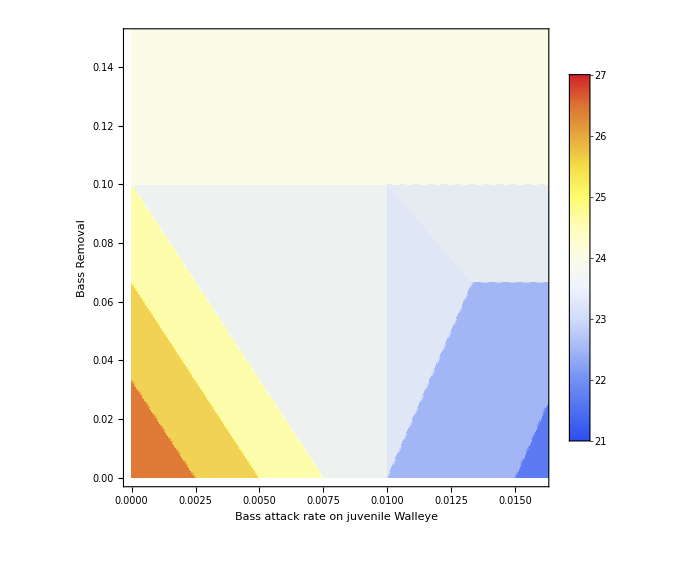

```mathematica
Clear[plot1e] (*same plot as above, just different axes*)
plot1e = ListDensityPlot[extdata1e, 
Mesh->5,FrameLabel->{{"Bass Removal"},{"Bass attack rate on juvenile Walleye"}},ColorFunction-> "TemperatureMap",ColorFunctionScaling -> True, PlotRange->{{0,0.016},{0,0.15}},
PlotLegends-> BarLegend[{"TemperatureMap",{21,27}}],MeshFunctions->{Function[{x,y,z},z]},MeshStyle->Directive[Dashed,Gray],ImageSize->Large, LabelStyle->Directive[FontSize->20,FontFamily->"Arial", FontColor->Black]]
```

## Time series

Changing temp doesn’t seem to do anything to the time series and I don’t get why.

```mathematica
Manipulate[Module[{R2sol,R1sol,C1sol,J1sol,P1sol,P2sol},
  {R2sol,R1sol,C1sol,J1sol,P1sol,P2sol} = NDSolveValue[
  PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.params/.rates/.T->Tin,
  {R2,R1,C1,J1,P1,P2},{t,0,1000}, MaxStepSize->0.05, MaxSteps->500000];
  Plot[{R2sol[t],R1sol[t],C1sol[t],J1sol[t],P1sol[t],P2sol[t]},{t,0,100}, PlotStyle->{{Red,Dashed},{Blue,Dashed},Yellow, Green, Black,{Purple, Dashed}},PlotRange->All, PlotLegends-> "Expressions"]],
  {{Tin,25},15,40,2}
  ]
```

```mathematica
sol=NDSolve[PdSystem[{1.0,1.0,1.0,1.0,1.0,1.0}]/.T1->10.0/.params/.rates,{R2,R1,R2,J1,P1,P2},{t,4000,5000},AccuracyGoal->70,MaxStepSize->0.05,MaxSteps->500000];
```

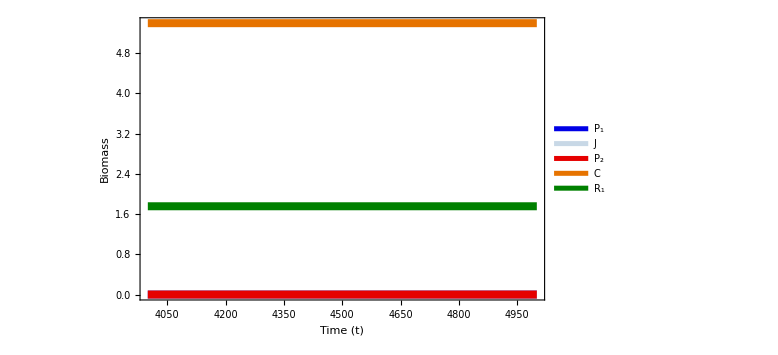

```mathematica
Plot[Evaluate[{P1[t],J1[t],P2[t],R2[t],R1[t]}/.sol],{t,4000,5000}, PlotLegends-> {"P_1","J","P_2","C","R_1"}, Frame->True, ImageSize->Large, 
PlotStyle->{{Thickness[0.01],Darker[Blue, 0.1]},{Thickness[0.01],Darker[LightBlue, 0.1]},{Thickness[0.01],Darker[Red, 0.1]},{Thickness[0.01],Darker[Orange, 0.1]},{Thickness[0.01],Darker[Green, 0.5]}},
FrameLabel->{"Time (t)","Biomass","",""},LabelStyle->Directive[FontSize->20, Bold, FontFamily->"Times"]]
```

## Additional Notes (notes have not been updated as of May 23, 2023)